# Mathematica Supplement A: SIRS model with Classic Matching Alleles Model

Joint coevolutionary-epidemiological models dampen Red Queen cycles and alter conditions for epidemics,  Ailene MacPherson and Sarah P. Otto, Theoretical Population Biology.

## Matching Alleles Model

```mathematica
Clear["Global`*"];
```

Here we derive a classic single locus matching alleles model of host parasite coevolution, determine the equilibrium allele frequencies in the host and parasite, and assess the stability of these equilibria to determine long term dynamics.

The Differential Equations

#### The Host Equation

Let ρ[i,t] be the probability that a host of type i is infected in the unit of time from t to t+Δt

```mathematica
ρ[i_,t_]:=Δt(β[i,1]pP[t]+β[i,2](1-pP[t]))
```

Here β[i,j] is the probability that a host of type i is infected with a pathogen of type j, where pP[t] equals the frequency of the type 1 pathogen.  
The resulting absolute fitness of type i host is

```mathematica
WH[i_,t_]:=1-ξH ρ[i,t]
```

Here ξH is the fitness cost to the host of infection.
The frequency of type 1 host (pH) at time t+Δt is therefore given by:

```mathematica
pH[t+Δt]=(pH[t]WH[1,t])/(pH[t]WH[1,t]+(1-pH[t])WH[2,t])//Simplify
```

(pH[t] (-1+Δt ξH pP[t] (β[1,1]-β[1,2])+Δt ξH β[1,2]))/(-1+Δt ξH pP[t] (β[2,1]-β[2,2])+Δt ξH β[2,2]+Δt ξH pH[t] (β[1,2]-β[2,2]+pP[t] (β[1,1]-β[1,2]-β[2,1]+β[2,2])))

Using the definition of the derivative the differential equation describing the change in host allele frequency (d/dt pH[t]) is given by:

```mathematica
Limit[(pH[t+Δt]-pH[t])/Δt,Δt->0]//Simplify
```

ξH (-1+pH[t]) pH[t] (β[1,2]-β[2,2]+pP[t] (β[1,1]-β[1,2]-β[2,1]+β[2,2]))

Rewriting this we have

```mathematica
f1[t_]:=-ξH (1-pH[t]) pH[t] ((1-pP[t])(β[1,2]-β[2,2])+pP[t] (β[1,1]-β[2,1]))
```

#### The Pathogen Equation

Let the probability that a pathogen of type i infects a host in the time t to t+Δt be η[i,t+Δt]

```mathematica
η[i_,t_]:=Δt(β[1,i]pH[t]+β[2,i](1-pH[t]))
```

The absolute fitness of pathogen type i is

```mathematica
WP[i_]:=1+ξP η[i,t]
```

Here ξP is the fitness benefit to the pathogen of infection.
The resulting frequency of type 1 pathogens at time t+Δt is:

```mathematica
pP[t+Δt]=(pP[t]WP[1])/(pP[t]WP[1]+(1-pP[t])WP[2])//Simplify
```

(pP[t] (1+Δt ξP (pH[t] (β[1,1]-β[2,1])+β[2,1])))/(pP[t] (1+Δt ξP (pH[t] (β[1,1]-β[2,1])+β[2,1]))+(1-pP[t]) (1+Δt ξP (pH[t] (β[1,2]-β[2,2])+β[2,2])))

Using the definition of the derivative, the differential equation for the change in pathogen allele frequency (d/dt pP[t]) is

```mathematica
Limit[(pP[t+Δt]-pP[t])/Δt,Δt->0]//Simplify
```

-ξP (-1+pP[t]) pP[t] (β[2,1]-β[2,2]+pH[t] (β[1,1]-β[1,2]-β[2,1]+β[2,2]))

Rewriting this

```mathematica
f2[t_]:=ξP (1-pP[t]) pP[t] ((1-pH[t])(β[2,1]-β[2,2])+pH[t] (β[1,1]-β[1,2]))
```

#### The System of differential equations

```mathematica
f1[t_]:=-ξH (1-pH[t]) pH[t] ((1-pP[t])(β[1,2]-β[2,2])+pP[t] (β[1,1]-β[2,1]))
f2[t_]:=ξP (1-pP[t]) pP[t] ((1-pH[t])(β[2,1]-β[2,2])+pH[t] (β[1,1]-β[1,2]))
```

```mathematica
ODEs[t_]:={D[pH[t],t]==f1[t],D[pP[t],t]==f2[t]}/.βsub;
```

To simplify the analysis we assume that we have a symmetric matching model where infection from either pathogen to the matching host is the same,  β[1,1]=β[2,2]=X, as is the probability of infection to a non-matching host, β[1,2]=β[2,1]=Y

```mathematica
βsub={β[1,1]->X,β[1,2]->Y,β[2,1]->Y,β[2,2]->X};
```

Equilibria

Let pHe and pPe be the host and pathogen allele frequencies at equilibrium, then the following two equations can be satisfied at equilibrium

```mathematica
EquiEqus={-ξH (1-pHe) pHe ((1-pPe)(β[1,2]-β[2,2])+pPe (β[1,1]-β[2,1]))==0,ξP (1-pPe) pPe ((1-pHe)(β[2,1]-β[2,2])+pHe (β[1,1]-β[1,2]))==0};
```

Solving for the equilibria gives:

```mathematica
Equilibria=Solve[EquiEqus,{pHe,pPe}]//Simplify
```

{{pHe→0,pPe→0},{pHe→1,pPe→0},{pHe→0,pPe→1},{pHe→1,pPe→1},{pHe→(-β[2,1]+β[2,2])/(β[1,1]-β[1,2]-β[2,1]+β[2,2]),pPe→(-β[1,2]+β[2,2])/(β[1,1]-β[1,2]-β[2,1]+β[2,2])}}

Under the special case of symmetry given by βsub these simplify to:

```mathematica
Equilibria=Equilibria/.βsub//Simplify
```

{{pHe→0,pPe→0},{pHe→1,pPe→0},{pHe→0,pPe→1},{pHe→1,pPe→1},{pHe→1/2,pPe→1/2}}

Hence the polymorphic equilibrium under the symmetric matching model is {1/2,1/2}.

Stability

The stability of the polymorphic {pHe→1/2,pPe→1/2} can be assessed using the Jacobian matrix evaluated at this equilibrium

```mathematica
Jmtrx={{D[f1[t],pH[t]],D[f1[t],pP[t]]},{D[f2[t],pH[t]],D[f2[t],pP[t]]}}/.βsub/.{pH[t]->1/2,pP[t]->1/2}//Simplify
```

{{0,-1/2 (X-Y) ξH},{1/2 (X-Y) ξP,0}}

```mathematica
Eigenvalues[Jmtrx]
```

{-1/2 ⅈ (X-Y) √ξH √ξP,1/2 ⅈ (X-Y) √ξH √ξP}

Because ξH and ξP are both positive, both eigenvalues are purely imaginary, implying that the system is neutrally stable about this endemic equilibrium.

Numerical Integration

We can numerically integrate system f1[t],f2[t] to confirm that the cycles are indeed stable.  We do so for the parameters given in Pars and initial conditions given by Inits

```mathematica
Pars={ξH->0.14,ξP->1,X->0.5,Y->0.25,tmax->1000};
```

```mathematica
Inits={pH[0]==0.6,pP[0]==0.3};
```

```mathematica
nsol=NDSolve[Join[ODEs[t],Inits]/.Pars,{pH[t],pP[t]},{t,0,tmax/.Pars}]//Flatten
pHsol[τ_]:=pH[t]/.nsol/.{t->τ}
pPsol[τ_]:=pP[t]/.nsol/.{t->τ}
```

{pH[t]→InterpolatingFunction[{{0.,1000.}},<>][t],pP[t]→InterpolatingFunction[{{0.,1000.}},<>][t]}

Here we plot host allele frequency is shown in black and pathogen allele frequency in green.

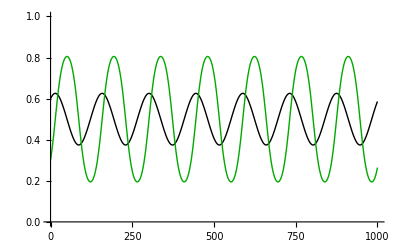

```mathematica
AFPlot=Plot[{pHsol[t],pPsol[t]},{t,0,tmax/.Pars},PlotStyle->{{Thick,Black},{Thick,Darker[Green]}},AxesStyle->Bold,PlotRange->{0,1}]
```

## SIRS Model without Coevolution

```mathematica
Clear["Global`*"];
```

Here we derive an SIRS model without host or pathogen genetic variation that exhibits a range of epidemiological dynamics.  We identify the equilibria of this model and then assess the stability of these equilibria to determine the long term epidemiological dynamics.

The Differential Equations

Let F1[0,t_]= d/dt s[0,t] be the rate of change in the susceptible host population density at time t. In the absence of genetic variation within the host population, we have only one type of host, which we label “0”, as a placeholder.

```mathematica
F1[0,t_]:=b(s[0,t]+∑_(j=1)^nI (i[j,t])+∑_(j=1)^nR (r[j,t]))(1-κ(s[0,t]+∑_(j=1)^nI (i[j,t])+∑_(j=1)^nR (r[j,t])))-d s[0,t]+nR/τR r[nR,t]-β s[0,t]∑_(j=1)^nI (i[j,t])
```

Here i[c,t] is the density of infected hosts in class c, and r[c,t] is the density of recovered hosts in class c at time t.  The rate of infection of susceptible hosts upon contact with an infection is β, the birth rate is b, d is the death rate of uninfected hosts, κ is the inverse of the carrying capacity, the number of recovered classes is given by nR, and the expected time spent in the recovered compartment τR. 

The differential equation for the density of infected hosts in class c, F2[c,t]=d/dt i[c,t].  Note that infections must start in class “1” and then progress through the later classes, hence F2[1,t] has a fundamentally different form from F2[c,t] for c>1.

```mathematica
F2[c_,t_]:=If[c==1,β s[0,t]∑_(j=1)^nI (i[j,t])-(δ+nI/τI)i[c,t],nI/τI i[c-1,t]-(δ+nI/τI)i[c,t]]
```

Here nI is the number of infectious classes, τI is the average time spent infected and δ is the death rate of infected individuals such that δ-d is a measure of pathogen virulence.

The differential equation for the recovered hosts, d/dt r[c,t]=F3[c,t].  Note that recovered individuals must start in class “1” and then progress through the later classes, hence F3[1,t] has a different form from F3[c,t] for c>1.

```mathematica
F3[c_,t_]:=If[c==1,nI/τI i[nI,t]-(d+nR/τR)r[c,t],nR/τR r[c-1,t]-(d+nR/τR)r[c,t]]
```

```mathematica
F3[c_,t_]:=If[c==1,nI/τI i[nI,t]-(d+nR/τR)r[c,t],nR/τR r[c-1,t]-(d+nR/τR)r[c,t]]
```

#### System of differential equations

The complete system of differential equations for a given nI and nR are given by the following list

```mathematica
ODEs[nIs_,nRs_]:=Block[{nI,nR,j,equs},equs={};nI=nIs;nR=nRs;
AppendTo[equs,D[s[0,t],t]==F1[0,t]];
For[j=1,j≤ nI,j++,AppendTo[equs,D[i[j,t],t]==F2[j,t]]];
For[j=1,j≤ nR,j++,AppendTo[equs,D[r[j,t],t]==F3[j,t]]];
equs
]
```

The list of variables for this system are

```mathematica
Vars[nIs_,nRs_]:=Block[{nI,nR,j,vars},vars={};nI=nIs;nR=nRs;
AppendTo[vars,s[0,t]];
For[j=1,j≤ nI,j++,AppendTo[vars,i[j,t]]];
For[j=1,j≤ nR,j++,AppendTo[vars,r[j,t]]];
vars
]
```

Equilibria

The system of equations above at equilibrium (denoted by se, ie[c], and re[c]) can be simplified greatly by solving for re[c] and ie[j] with j>1 in terms of ie[1].  Specifically at equilibrium

re[c]:=(nR/τR)(τR/(nR+d τR))re[c-1] for c>1 and re[1]:=(nI/τI)(τR/(nR+d τR))ie[nI]
ie[c]:=(nI/τI)(τI/(nI+δ τI))ie[c-1] for c>1

Hence

```mathematica
re[c_]:=((nR/(nR+d τR)))^(c-1)(nI/τI(τR/(nR+d τR)))((nI/(nI+δ τI)))^(nI-1)ie[1]
```

for c={1,2...nR} and

```mathematica
ie[c_]:=If[c>1,((nI/(nI+δ τI)))^(c-1)ie[1],ie1]
```

for c={1,2...nI}.

The remaining two equations that must be satisfied at equilibrium are F1[0,t]==0, and F2[1,t]==0.  Using the above equations for re[c] and ie[c] we can express these remaining two equations in terms of the density of susceptible hosts (se) and the density of infected hosts in the first class (ie[1]=ie1) by defining zI (the sum of all infected classes, relative to the number in the first infected class), zR (the sum of all recovered classes, relative to the number in the first infected class), and znR (the number in the last recovered class, relative to the number in the first infected class):

```mathematica
zsub={zI->Sum[ie[c],{c,1,nI}]/ie[1],zR->Sum[re[c],{c,1,nR}]/ie[1],znR->re[nR]/ie[1]}//Simplify
```

{zI→(nI+δ τI-nI^nI (nI+δ τI)^(1-nI))/(δ τI),zR→-(nI (nI/(nI+δ τI))^(-1+nI) (-1+(nR/(nR+d τR))^nR))/(d τI),znR→(nI (nI/(nI+δ τI))^(-1+nI) τR (nR/(nR+d τR))^nR)/(nR τI)}

The remaining two equations that must be satisfied are

```mathematica
EquiEqus={F1[0,t]==0,F2[1,t]==0}/.{∑_(j=1)^nI i[j,t]->zI ie1,∑_(j=1)^nR r[j,t]->zR ie1,r[nR,t]->znR ie1,i[1,t]->ie1,s[0,t]->se}
```

{-d se-ie1 se zI β+b (se+ie1 zI+ie1 zR) (1-(se+ie1 zI+ie1 zR) κ)+(ie1 nR znR)/τR==0,ie1 se zI β-ie1 (δ+nI/τI)==0}

```mathematica
Equilibria=Solve[EquiEqus,{se,ie1}]//Simplify
```

{{se→0,ie1→0},{se→(b-d)/(b κ),ie1→0},{se→(nI+δ τI)/(zI β τI),ie1→-1/(2 b zI^2 (zI+zR)^2 β^2 κ τI^2 τR)(-nR zI^2 znR β^2 τI^2+nI zI^2 β^2 τI τR+2 b nI zI^2 β κ τI τR+2 b nI zI zR β κ τI τR-b zI^3 β^2 τI^2 τR-b zI^2 zR β^2 τI^2 τR+zI^2 β^2 δ τI^2 τR+2 b zI^2 β δ κ τI^2 τR+2 b zI zR β δ κ τI^2 τR+√(zI^2 β^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d zI β τI+b (nI κ-zI β τI+δ κ τI)) τR^2+(nR zI znR β τI-(nI (2 b zR κ+zI (β+2 b κ))+(zI β δ-b (zI+zR) (zI β-2 δ κ)) τI) τR)^2)))},{se→(nI+δ τI)/(zI β τI),ie1→1/(2 b zI^2 (zI+zR)^2 β^2 κ τI^2 τR)(nR zI^2 znR β^2 τI^2-nI zI^2 β^2 τI τR-2 b nI zI^2 β κ τI τR-2 b nI zI zR β κ τI τR+b zI^3 β^2 τI^2 τR+b zI^2 zR β^2 τI^2 τR-zI^2 β^2 δ τI^2 τR-2 b zI^2 β δ κ τI^2 τR-2 b zI zR β δ κ τI^2 τR+√(zI^2 β^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d zI β τI+b (nI κ-zI β τI+δ κ τI)) τR^2+(nR zI znR β τI-(nI (2 b zR κ+zI (β+2 b κ))+(zI β δ-b (zI+zR) (zI β-2 δ κ)) τI) τR)^2)))}}

Given se and ie1, the following function of nI and nR gives the substitution list for the equilibrium number of the variable “num”

```mathematica
EquiSub[nIs_,nRs_,num_]:=Block[{nI,nR,j,sub},nI=nIs;nR=nRs;sub={};
AppendTo[sub,s[0,t]->se ];AppendTo[sub,i[1,t]->ie1 ];
For[j=2,j≤nI,j++,AppendTo[sub,i[j,t]->(nI/τI(τI/(nI+δ τI)))^(j-1) ie1]];
For[j=1,j≤nR,j++,AppendTo[sub,r[j,t]->(nR/τR(τR/(nR+d τR)))^(j-1)(nI/τI(τR/(nR+d τR)))(nI/τI(τI/(nI+δ τI)))^(nI-1) ie1]];
sub=sub/.Equilibria[[num]]/.zsub
]
```

The first equilibrium is host extinction the second equilibrium is disease extinction, the third and fourth equilibria are both potentially endemic equilibria although only one will be biologically plausible, as proven next.

#### Biological Validity of Endemic Equilibrium

From the derivation of the endemic equilibria above we know that it must satisfy the following quadratic equation in terms of ie1.

```mathematica
Collect[EquiEqus[[1]]/.Flatten[Solve[EquiEqus[[2]],se]],ie1]
```

ie1^2 (-b zI^2 κ-2 b zI zR κ-b zR^2 κ)+(b (nI+δ τI))/(zI β τI)-(d (nI+δ τI))/(zI β τI)-(b κ (nI+δ τI)^2)/(zI^2 β^2 τI^2)+ie1 (b zI+b zR-(nI+δ τI)/τI-(2 b κ (nI+δ τI))/(β τI)-(2 b zR κ (nI+δ τI))/(zI β τI)+(nR znR)/τR)==0

Our goal is to show that at most one root is biologically valid, ie positive and real. Dividing through by the coefficient of ie1^2 guarantees that we have an up-wards facing parabola.

```mathematica
Quad[ie1_]:=Collect[1/(-b zI^2 κ-2 b zI zR κ-b zR^2 κ)(ie1^2 (-b zI^2 κ-2 b zI zR κ-b zR^2 κ)+(b (nI+δ τI))/(zI β τI)-(d (nI+δ τI))/(zI β τI)-(b κ (nI+δ τI)^2)/(zI^2 β^2 τI^2)+ie1 (b zI+b zR-(nI+δ τI)/τI-(2 b κ (nI+δ τI))/(β τI)-(2 b zR κ (nI+δ τI))/(zI β τI)+(nR znR)/τR)),ie1,Simplify]
Quad[ie1]
```

ie1^2+((nI+δ τI) (d zI β τI+b (nI κ-zI β τI+δ κ τI)))/(b zI^2 (zI+zR)^2 β^2 κ τI^2)+(ie1 (-nR zI znR β τI+(nI (2 b zR κ+zI (β+2 b κ))+(zI β δ-b (zI+zR) (zI β-2 δ κ)) τI) τR))/(b zI (zI+zR)^2 β κ τI τR)

We can show that one equilibrium is biologically valid and the other not by using the following logic:

If the constant term of the quadratic is negative then we are guaranteed that one root is positive (biologically valid) and one root is negative (not-biologically valid).  If the constant term of the quadratic is positive then there are three possibilities: 1) both roots are negative, this will occur if the slope of the quadratic at 0 is positive, 2) both roots are positive, this will occur if the slope of the quadratic at 0 is negative, and 3) there are no real roots.  We begin by identifying the conditions for which the constant term is negative.

Conditions for a negative constant term: Exactly one biologically valid equilibrium.

There will be exactly one biologically valid equilibrium if the constant term (((nI+δ τI) (d zI β τI+b (nI κ-zI β τI+δ κ τI)))/(b zI^2 (zI+zR)^2 β^2 κ τI^2)) is negative.  Given that (nI+δ τI)>0 the critical value of β for this to occur is given by:

```mathematica
Solve[(d zI β τI+b (nI κ-zI β τI+δ κ τI))==0,β]/.zsub//Simplify//Flatten
```

{β→(b δ κ (nI+δ τI)^nI)/((b-d) (-nI^nI+(nI+δ τI)^nI))}

If β is greater than this critical value than there will be only one real root. If not there are three possibilities, either both equilibria are positive (this can only occur if the slope at ie1=0 is negative), both equilibria are negative (this can only occur if the slope at ie1=0 is positive), or both equilibria are complex.  To exclude the possibility that both equilibria are positive and hence biologically valid below we show that for a large number of parameter combinations the slope of the quadratic at ie1=0 is positive.

Conditions under which neither equilibrium is biologically valid

```mathematica
Slope=(-nR zI znR β τI+(nI (2 b zR κ+zI (β+2 b κ))+(zI β δ-b (zI+zR) (zI β-2 δ κ)) τI) τR)/(b zI (zI+zR)^2 β κ τI τR)/.zsub;
```

```mathematica
Module[{nIs,nRs,τIs,τRs,bs,ds,δs,βs,c,parsSub},NegList={};PosList={};
For[c=1,c≤5000,c++,
(*Drawing values*)
nIs=Random[Integer,{1,50}];nRs=Random[Integer,{1,50}];
τIs=Random[Real,{1,40}];τRs=Random[Real,{20,100}];
bs=Random[Real,{0.01,0.2}];ds=Random[Real,{0.001,bs}];δs=Random[Real,{ds,ds+0.1}];
parsSub={nI->nIs,nR->nRs,τI->τIs,τR->τRs,b->bs,d->ds,δ->δs,β->1,κ->1};
βs=Random[Real,{0.01,(b δ κ (nI+δ τI)^nI)/((b-d) (-nI^nI+(nI+δ τI)^nI))/.parsSub}];
parsSub={nI->nIs,nR->nRs,τI->τIs,τR->τRs,b->bs,d->ds,δ->δs,β->βs,κ->1};test=(Slope/.parsSub);
If[test<0,AppendTo[NegList,{nIs,nRs,τIs,τRs,bs,ds,δs,βs,test}],AppendTo[PosList,{nIs,nRs,τIs,τRs,bs,ds,δs,βs,test}]]
]
]
```

```mathematica
NegList
```

{}

```mathematica
Length[PosList]
```

5000

Out of the 5000 randomly drawn parameter combinations for which the y intercept is greater than 0 the slope is always positive indicating that both roots are either negative or complex.

Stability

The stability of the system can be assessed by computing the eigenvalues of the Jacobian matrix.

```mathematica
Jmtrx[nIs_,nRs_]:=Block[{c,j,nI,nR,jmtrx}, nI=nIs;nR=nRs;jmtrx=Table[{},{j,1,1+nI+nR}];
(*Susceptible Equation*)
AppendTo[jmtrx[[1]],D[F1[0,t],s[0,t]]];(*Susceptible Derivative*)
For[j=1,j≤nI,j++,AppendTo[jmtrx[[1]],D[F1[0,t],i[j,t]] ]];(*Infected class j Derivative*)
For[j=1,j≤nR,j++,AppendTo[jmtrx[[1]],D[F1[0,t],r[j,t]] ]];(*Recovered class j Derivative*)
(*Infected class c Equation*)
For[c=1,c≤ nI,c++,
AppendTo[jmtrx[[1+c]],D[F2[c,t],s[0,t]]];(*Susceptible Derivative*)
For[j=1,j≤nI,j++,AppendTo[jmtrx[[1+c]],D[F2[c,t],i[j,t]] ]];(*Infected class j Derivative*)
For[j=1,j≤nR,j++,AppendTo[jmtrx[[1+c]],D[F2[c,t],r[j,t]] ]];(*Recovered class j Derivative*)
];
(*Recovered class c Equation*)
For[c=1,c≤nR,c++,
AppendTo[jmtrx[[1+nI+c]],D[F3[c,t],s[0,t]]];(*Susceptible Derivative*)
For[j=1,j≤nI,j++,AppendTo[jmtrx[[1+nI+c]],D[F3[c,t],i[j,t]] ]];(*Infected class j Derivative*)
For[j=1,j≤nR,j++,AppendTo[jmtrx[[1+nI+c]],D[F3[c,t],r[j,t]] ]];(*Recovered class j Derivative*)
];
jmtrx
]
```

Although we cannot find the eigenvalues of this matrix analytically in all cases we can do so numerically to assess the stability of each equilibria for a given parameter set (Pars).  In addition we determine the conditions under which the extinction and disease extinction equilibria are unstable.

```mathematica
Pars={nI->4,nR->4,τI->8,τR->40,β->0.5,b->0.02,d->0.001,δ->0.01,κ->1};
```

#### Extinction equilibria

Numerically finding the eigenvalues at the extinction equilibrium

```mathematica
λs=Eigenvalues[N[Jmtrx[nI/.Pars,nR/.Pars]/.EquiSub[nI/.Pars,nR/.Pars,1]]/.Pars]
```

{-0.51,-0.51,-0.51,-0.51,-0.101,-0.101,-0.101,-0.101,0.019}

The presence of a postive eigenvalue ensures this equilibrium is unstable.  We can show that this holds in general due to the simplicity of the jacobian matrix at this equilibrium.  Specifically the charateristic polynomial for eigenvalue λ is given by:

```mathematica
CharPoly[λ_]:=(b-d-λ)(nI/τI+δ+λ)^nI(nR/τR+d+λ)^nR
```

Hence there is one root at λ=d-b, nI roots at λ=-(nI/τI+δ) and nR roots at λ=-(nR/τR+d).  Roots λ=-(nI/τI+δ) and λ=-(nR/τR+d) are guaranteed to be negative but λ=d-b is negative, and hence the equilibrium stable, only when d>b.

#### Disease free equilibria

Here we determine where the disease free equilibrium transitions from being stable to unstable. In other words we find the pont at which the leading eigenvalue of the Jacobian matrix evaluated at this equilibrium is 0.  In particular we conjecture that this point will be the same as the point at which only one endemic equilibrium is biologically valid (see equilbirum section).

If we let AA=d/ds(d/dt s(t)) and JJ=d/dr_c(d/dt r_c(t)) evaluated at the disease free equilibrium (AA=-b+b (1-(b-d)/b), JJ=-d-2/τR) then the charateristic polynomial of the Jacobian of the full system is given by (AA-λ)(JJ-λ)^nR Det[M[nI]] where M[nI] is as follows:

```mathematica
M[nIs_]:=Block[{nI,mtrx,j},nI=nIs;mtrx=Table[0,{r,1,nI},{c,1,nI}];
mtrx[[1,1]]=EE-λ;
For[j=2,j≤ nI,j++,mtrx[[1,j]]=FF];
For[c=2,c≤nI,c++,mtrx[[c,c-1]]=GG;mtrx[[c,c]]=HH-λ;
];
mtrx
]
```

For example when nI=5

```mathematica
MatrixForm[M[5]]
```

(EE-λ | FF | FF | FF | FF
GG | HH-λ | 0 | 0 | 0
0 | GG | HH-λ | 0 | 0
0 | 0 | GG | HH-λ | 0
0 | 0 | 0 | GG | HH-λ)

Since neither AA or JJ are zero for the for Det[M[nI]] to have a zero root the constnat term of this polynomial must be zero.  To show this we first write the recursion equation for the constant term:

```mathematica
Sre[nI_]:=If[nI>2,FF (-GG)^(nI-1)+HH Sre[nI-1],-FF GG+EE HH]
```

Where the letters are given by:

```mathematica
letters={EE-> -δ+((b-d) β)/(b κ)-nI/τI,FF-> ((b-d) β)/(b κ),GG-> nI/τI,HH-> -δ-nI/τI};
```

The recursion equation Sre[nI] can be in turn be rewriten as the following:

```mathematica
S[nI_]:=FF Sum[(-GG)^i(HH)^(nI-1-i),{i,1,nI-1}]+EE HH^(nI-1)
```

Below we show that, under the same conditions that ensured that only one endemic equilibrium was biologically valid (β→(b δ κ (nI+δ τI))/((b-d) (nI+δ τI-nI^nI (nI+δ τI)^(1-nI)))) the jacobian matrix has a zero root.

```mathematica
Simplify[S[nI]/.letters/.β->(b δ κ (nI+δ τI))/((b-d) (nI+δ τI-nI^nI (nI+δ τI)^(1-nI))),{nI>0,δ>0,τI>0}]
```

0

Although the appearance of a zero root does not guarantee that the system does not have a (+) root and hence is unstable we at least know that several of the roots λ=AA and λ=JJ are negative and numerically we have yet to find a case where this zero root is not the leading eigenvalue.

The criterian for a zero root (β→(b δ κ (nI+δ τI))/((b-d) (nI+δ τI-nI^nI (nI+δ τI)^(1-nI)))) has another implication.  Substituting in se=(b-d)/bkwe can rearrange to get an expression for the critical density of susceptible individuals necessary for disease spread, this is similar to the expression for R0=1

```mathematica
Solve[β==(δ  (nI+δ τI))/(se(nI+δ τI-nI^nI (nI+δ τI)^(1-nI))),se]//Flatten//Simplify
```

{se→(δ (nI+δ τI)^nI)/(β (-nI^nI+(nI+δ τI)^nI))}

#### Endemic Equilibrium 1

First we evaluate the equilibrium to ensure that it is biologically plausible (all variables have value greater than 0).

```mathematica
EquiSub[nI/.Pars,nR/.Pars,3]/.Pars
```

{s[0,t]→0.262624,i[1,t]→-0.0128283,i[2,t]→-0.0125767,i[3,t]→-0.0123301,i[4,t]→-0.0120884,r[1,t]→-0.0598434,r[2,t]→-0.0592509,r[3,t]→-0.0586643,r[4,t]→-0.0580834}

Not biologically valid

```mathematica
λs=Eigenvalues[N[Jmtrx[nI/.Pars,nR/.Pars]/.EquiSub[nI/.Pars,nR/.Pars,3]]/.Pars]
```

{-0.81408,-0.54493+0.320287 ⅈ,-0.54493-0.320287 ⅈ,-0.160935+0.0482506 ⅈ,-0.160935-0.0482506 ⅈ,-0.0701044+0.0772022 ⅈ,-0.0701044-0.0772022 ⅈ,0.0807299,0.0174347}

```mathematica
Max[Re[λs]]
```

0.0807299

The presence of a (+) eigenvalue denotes an unstable equilibria (which is not surprising given that it is unrealistic)

#### Endemic Equilibrium 2

First we evaluate the equilibrium to ensure that it is biologically plausible (all variables have value greater than 0).

```mathematica
EquiSub[nI/.Pars,nR/.Pars,4]/.Pars
```

{s[0,t]→0.262624,i[1,t]→0.028378,i[2,t]→0.0278215,i[3,t]→0.027276,i[4,t]→0.0267412,r[1,t]→0.132382,r[2,t]→0.131071,r[3,t]→0.129774,r[4,t]→0.128489}

This equilibria is biologically valid

```mathematica
λs=Eigenvalues[N[Jmtrx[nI/.Pars,nR/.Pars]/.EquiSub[nI/.Pars,nR/.Pars,4]]/.Pars]
```

{-0.820143,-0.549971+0.326902 ⅈ,-0.549971-0.326902 ⅈ,-0.18895,-0.115445+0.0934369 ⅈ,-0.115445-0.0934369 ⅈ,-0.0134394+0.110992 ⅈ,-0.0134394-0.110992 ⅈ,-0.0177746}

```mathematica
Max[Re[λs]]
```

-0.0134394

Since all eigenvalues are (-) the equilibrium is stable with damped cycles (complex eigenvalue with (-) real part)

Numerical Integration

We can numerically integrate the system of differential equations to confirm the stability results above for a particular set of initial conditions given by inits[nI,nR]

```mathematica
Pars={nI->20,nR->20,τI->14,τR->33,β->0.5,b->0.02,d->0.001,δ->0.01,κ->1,tmax->1000};
```

In particular the initial conditions used here are the second (biologically valid) endemic equilibrium with a small perturbation.

```mathematica
Inits[nIs_,nRs_]:=Block[{nI,nR,j,inits},inits={};nI=nIs;nR=nRs;
AppendTo[inits,s[0,0]==(0.8)s[0,t]];
For[j=1,j≤nI,j++,
AppendTo[inits,i[j,0]==(1.05)i[j,t]];
];
For[j=1,j≤nR,j++,
AppendTo[inits,r[j,0]==(1.00)r[j,t]];
];
inits/.EquiSub[nI,nR,4]
]
```

```mathematica
nsol=NDSolve[Join[ODEs[nI/.Pars,nR/.Pars],Inits[nI/.Pars,nR/.Pars]]/.Pars,Vars[nI/.Pars,nR/.Pars],{t,0,tmax/.Pars}]//Flatten;
ssol[0,τ_]:=s[0,t]/.nsol/.{t->τ};
isol[c_,τ_]:=i[c,t]/.nsol/.{t->τ};
rsol[c_,τ_]:=r[c,t]/.nsol/.{t->τ};
```

Here we show the number of susceptible individuals (red), the total number of infected individuals (blue), and the total number of recovered individuals (purple).

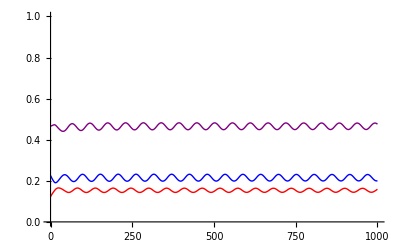

```mathematica
SIRSPlot=Plot[{ssol[0,t],Sum[isol[c,t],{c,1,nI/.Pars}],Sum[rsol[c,t],{c,1,nR/.Pars}]},{t,0,tmax/.Pars},PlotRange->{0,1},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Purple}},AxesStyle->Bold]
```

## SIRS Model with Matching Alleles Coevolution

```mathematica
Clear["Global`*"];
```

Here we combine the models of the previous two sections in an SIRS model with 2 host and 2 pathogen types witch interact in a matching-allele model type fashion.  We derive the equilibria of the resulting system and analyze their stability.

The Differential Equations

Let g1[h,t]= d/dt s[h,t] be the rate of change in the susceptible host population density at time t. We now allow for genetic variation within the host population, where “h” denotes the allele carried by the host (assumed to be inherited with perfect transmission, as in a haploid one-locus model or an asexual model). The host allele, h, can take on a value of 1 or 2.

```mathematica
g1[h_,t_]:=b(s[h,t]+∑_(l=1)^2 ∑_(j=1)^nI i[h,l,j,t]+∑_(j=1)^nR r[h,j,t])(1-κ(∑_(k=1)^2 s[k,t]+∑_(k=1)^2 ∑_(l=1)^2 ∑_(j=1)^nI i[k,l,j,t]+∑_(k=1)^2 ∑_(j=1)^nR r[k,j,t]))-d s[h,t]+nR/τR r[h,nR,t]-s[h,t]∑_(k=1)^2 ∑_(l=1)^2 ∑_(j=1)^nI (β[h,l]i[k,l,j,t])
```

Let g2[h,p,c,t]=d/dt i[h,p,c,t] be the rate of change of infected hosts in class c of type h infected with pathogen of type p, where p can take on values of 1 or 0. Note that newly infected hosts must start in state “1” and then progress through the later infection stages, hence g2[h,p,1,t] has a fundamentally different form from g2[h,p,c,t] for c>1.

```mathematica
g2[h_,p_,c_,t_]:=If[c==1,s[h,t]β[h,p]∑_(k=1)^2 ∑_(j=1)^nI (i[k,p,j,t])-(δ+nI/τI)i[h,p,c,t],nI/τI i[h,p,c-1,t]-(δ+nI/τI)i[h,p,c,t]]
```

Let g3[h,p,c,t]=d/dt r[h,c,t], the rate of change of infected hosts of type h in class c infected with pathogen of type p. Note that recovered individuals must start in state “1” and then progress through the later stages, hence g3[h,p,1,t] has a different form from g3[h,p,c,t] for c>1.

```mathematica
g3[h_,c_,t_]:=If[c==1,nI/τI ∑_(l=1)^2 i[h,l,nI,t]-(d+nR/τR)r[h,c,t],nR/τR r[h,c-1,t]-(d+nR/τR)r[h,c,t]]
```

To simplify the analysis we assume that we have a symmetric matching model where infection from either pathogen to the matching host is the same,  β[1,1]=β[2,2]=X, as is the probability of infection to a non-matching host, β[1,2]=β[2,1]=Y:

```mathematica
βsub={β[1,1]->X,β[1,2]->Y,β[2,1]->Y,β[2,2]->X};
```

The complete set of differential equations for a given nI and nR is given by:

```mathematica
ODEs[nIs_,nRs_]:=Block[{nI,nR,equs,h,p,c},equs={};nI=nIs;nR=nRs; 
For[h=1,h≤2,h++,
AppendTo[equs,D[s[h,t],t]==g1[h,t]];
];
For[h=1,h≤2,h++,
For[p=1,p≤2,p++,
For[c=1,c≤nI,c++,
AppendTo[equs,D[i[h,p,c,t],t]==g2[h,p,c,t]];
]
]
];
For[h=1,h≤2,h++,
For[c=1,c≤nR,c++,
AppendTo[equs,D[r[h,c,t],t]==g3[h,c,t]];
]
];
equs=equs/.βsub
]
```

Equilibria

Let se[h], ie[h,p,c] and re[h,c] be the values of s[h,t], i[h,p,c,t], and r[h,c,t] at equilibrium
Like the SIRS model without coevolution, by solving for re[h,c] and ie[h,p,c>1] in terms of ie[h,p,1], the system of equations that must be satisfied at equilibrium reduces down to only 6 equations.

Reducing the system of equations at Equilibrium

At Equilibrium, for c>1

re[h_,c_]:=nR/τR(τR/(d τR+nR))re[h,c-1]

For c=1

re[h,1]:=nI/τI(τR/(d τR+nR))∑_(p=1)^2 ie[h,p,nI]

similarly, for c>1

ie[h_,p_,c_]:=nI/τI(nI/(δ τI+nI))ie[h,p,c-1]

Substituting these equations into each other to express re[h,c] and ie[h,p,c] in terms of ie[h,p,1]=ie1[h,p] gives:

```mathematica
re[h_,c_]:=(nR/(d τR+nR))^(c-1)(nI/τI(τR/(d τR+nR)))(nI/(δ τI+nI))^(nI-1)∑_(l=1)^2 ie1[h,l]
ie[h_,p_,c_]:=(nI/(δ τI+nI))^(c-1)ie1[h,p]
```

We can then use these expression to write the equation for d/dt se[h]=0 and d/dt ie1[h,p]=0 in terms of ie1[h,p].  This is simplified by defining zI (the sum of all infected classes, relative to the number in the first infected class with the same h and p), zR (the sum of all recovered classes, relative to the number in the first infected class with the same h), and znR (the number in the last recovered class, relative to the number in the first infected class with the same h):

```mathematica
zsub={zI->Sum[ie[h,p,c],{c,1,nI}]/ie[h,p,1],zR->Sum[re[h,c],{c,1,nR}]/(ie[h,1,1]+ie[h,2,1]),znR->re[h,nR]/(ie[h,1,1]+ie[h,2,1])}//FullSimplify
```

{zI→-((nI+δ τI) (-1+(nI/(nI+δ τI))^nI))/(δ τI),zR→-(nI (nI/(nI+δ τI))^(-1+nI) (-1+(nR/(nR+d τR))^nR))/(d τI),znR→(nI (nI/(nI+δ τI))^(-1+nI) τR (nR/(nR+d τR))^nR)/(nR τI)}

The resulting system of 6 equations that must be satisfied at equilibrium are:

```mathematica
G1[h_]:=b(se[h]+(zI+zR)(ie1[h,1]+ie1[h,2]))(1-κ∑_(k=1)^2 (se[k]+(zI+zR)(ie1[k,1]+ie1[k,2])))-d se[h]+nR/τR znR(ie1[h,1]+ie1[h,2])-se[h]zI∑_(k=1)^2 ∑_(l=1)^2 (β[h,l]ie1[k,l])
G2[h_,p_]:=se[h]zI β[h,p]∑_(k=1)^2 (ie1[k,p])-(δ+nI/τI)ie1[h,p]
```

A resulting list of expressions that must equal zero at equilibrium

```mathematica
EquiList=Join[Table[G1[h],{h,1,2}],Table[G2[h,p],{h,1,2},{p,1,2}]]/.βsub//Flatten//Simplify
```

{(nR znR (ie1[1,1]+ie1[1,2]))/τR-d se[1]-zI (X (ie1[1,1]+ie1[2,1])+Y (ie1[1,2]+ie1[2,2])) se[1]+b ((zI+zR) (ie1[1,1]+ie1[1,2])+se[1]) (1-κ ((zI+zR) (ie1[1,1]+ie1[1,2])+(zI+zR) (ie1[2,1]+ie1[2,2])+se[1]+se[2])),(nR znR (ie1[2,1]+ie1[2,2]))/τR-d se[2]-zI (Y (ie1[1,1]+ie1[2,1])+X (ie1[1,2]+ie1[2,2])) se[2]+b ((zI+zR) (ie1[2,1]+ie1[2,2])+se[2]) (1-κ ((zI+zR) (ie1[1,1]+ie1[1,2])+(zI+zR) (ie1[2,1]+ie1[2,2])+se[1]+se[2])),-(δ+nI/τI) ie1[1,1]+X zI (ie1[1,1]+ie1[2,1]) se[1],-(δ+nI/τI) ie1[1,2]+Y zI (ie1[1,2]+ie1[2,2]) se[1],-(δ+nI/τI) ie1[2,1]+Y zI (ie1[1,1]+ie1[2,1]) se[2],-(δ+nI/τI) ie1[2,2]+X zI (ie1[1,2]+ie1[2,2]) se[2]}

The set of variables at equilibrium is:

```mathematica
EquiVars=Join[Table[s[h,∞]->se[h],{h,1,2}],Table[i[h,p,1,∞]->ie1[h,p],{h,1,2},{p,1,2}]]//Flatten//Simplify;
```

### Extinction equilibrium

Host extinction satisfies the equilibrium equations

```mathematica
EquiList/.{se[1]->0,se[2]->0,ie1[1,1]->0,ie1[1,2]->0,ie1[2,1]->0,ie1[2,2]->0}
```

{0,0,0,0,0,0}

```mathematica
EquiVars/.{se[1]->0,se[2]->0,ie1[1,1]->0,ie1[1,2]->0,ie1[2,1]->0,ie1[2,2]->0}
```

{s[1,∞]→0,s[2,∞]→0,i[1,1,1,∞]→0,i[1,2,1,∞]→0,i[2,1,1,∞]→0,i[2,2,1,∞]→0}

### Disease extinction

Let us search for equilibria with no infection types present

```mathematica
subB={ie1[1,1]->0,ie1[1,2]->0,ie1[2,1]->0,ie1[2,2]->0};
```

```mathematica
EquiList/.subB
```

{-d se[1]+b se[1] (1-κ (se[1]+se[2])),-d se[2]+b se[2] (1-κ (se[1]+se[2])),0,0,0,0}

solving equation 1 for se[1]

```mathematica
subse1=Solve[(EquiList/.subB)[[1]]==0,se[1]]
```

{{se[1]→0},{se[1]→(b-d-b κ se[2])/(b κ)}}

Option 1:  se[1]=0

```mathematica
EquiList/.subB/.subse1[[1]]
```

{0,-d se[2]+b se[2] (1-κ se[2]),0,0,0,0}

Solving equation 2 for se[2]

```mathematica
subse2=Solve[(EquiList/.subB/.subse1[[1]])[[2]]==0,se[2]]
```

{{se[2]→0},{se[2]→(b-d)/(b κ)}}

The first of these is the same as disease extinction. The second equilibrium value se[2]→((b-d) κ)/b satisfies the remaining equilibrium equations.

```mathematica
EquiList/.subB/.subse1[[1]]/.subse2[[2]]//Simplify
```

{0,0,0,0,0,0}

```mathematica
EquiVars/.subB/.subse1[[1]]/.subse2[[2]]
```

{s[1,∞]→0,s[2,∞]→(b-d)/(b κ),i[1,1,1,∞]→0,i[1,2,1,∞]→0,i[2,1,1,∞]→0,i[2,2,1,∞]→0}

Option 2: se[1]=(b-d-b κ se[2])/(b κ)

The second option for se[1] satisfies all the equilibrium equations

```mathematica
(EquiList/.subB/.subse1[[2]])//Simplify
```

{0,0,0,0,0,0}

```mathematica
EquiVars/.subB/.subse1[[2]]
```

{s[1,∞]→(b-d-b κ se[2])/(b κ),s[2,∞]→se[2],i[1,1,1,∞]→0,i[1,2,1,∞]→0,i[2,1,1,∞]→0,i[2,2,1,∞]→0}

### Single infection types present.

If we search for equilibria for which only a single infection type, ie1[h,p], is present there are two possibilities, either we have matching hosts and parasites (h=p) or non-matching (h≠p):

Option 1: h=p, ex ie1[1,1]≠0

```mathematica
subC1={ie1[1,2]->0,ie1[2,1]->0,ie1[2,2]->0};
```

```mathematica
EquiList/.subC1//Simplify
```

{(nR znR ie1[1,1])/τR-d se[1]-X zI ie1[1,1] se[1]+b ((zI+zR) ie1[1,1]+se[1]) (1-κ ((zI+zR) ie1[1,1]+se[1]+se[2])),se[2] (-d-Y zI ie1[1,1]+b (1-κ ((zI+zR) ie1[1,1]+se[1]+se[2]))),ie1[1,1] (-δ-nI/τI+X zI se[1]),0,Y zI ie1[1,1] se[2],0}

Solving equation 5 for se[2] (note that equation 5 is also satisfied by ie1[1,1]=0 which does not satisfy the assumption of this equilibrium search)

```mathematica
subse2=Solve[(EquiList/.subC1)[[5]]==0,se[2]]//Flatten
```

{se[2]→0}

```mathematica
EquiList/.subC1/.subse2//Simplify
```

{(nR znR ie1[1,1])/τR-d se[1]-X zI ie1[1,1] se[1]+b ((zI+zR) ie1[1,1]+se[1]) (1-κ ((zI+zR) ie1[1,1]+se[1])),0,ie1[1,1] (-δ-nI/τI+X zI se[1]),0,0,0}

Solving equation 3 for se[1]

```mathematica
subse1=Solve[(EquiList/.subC1/.subse2)[[3]]==0,se[1]]//Flatten
```

{se[1]→(nI+δ τI)/(X zI τI)}

```mathematica
EquiList/.subC1/.subse2/.subse1//Simplify
```

{-(d (nI+δ τI))/(X zI τI)-((nI+δ τI) ie1[1,1])/τI+(nR znR ie1[1,1])/τR-(b (nI+τI (δ+X zI (zI+zR) ie1[1,1])) (nI κ+τI (δ κ+X zI (-1+zI κ ie1[1,1]+zR κ ie1[1,1]))))/(X^2 zI^2 τI^2),0,0,0,0,0}

Solving equation 1 for ie1[1,1]

```mathematica
subie11=Solve[(EquiList/.subC1/.subse2/.subse1)[[1]]==0,ie1[1,1]]//Simplify//Flatten
```

{ie1[1,1]→1/(2 b X zI (zI+zR)^2 κ τI τR)(nR X zI znR τI-τR (nI (X zI+2 b (zI+zR) κ)-τI (b X zI^2+b X zI zR-X zI δ-2 b zI δ κ-2 b zR δ κ+X zI √(1/(X zI τI^2 τR^2)(nR^2 X zI znR^2 τI^2-2 nR znR τI (nI (X zI+2 b (zI+zR) κ)+(X zI δ-b (zI+zR) (X zI-2 δ κ)) τI) τR+(nI^2 (X zI+4 b (zI+zR) κ)-2 nI (-X zI δ+b (zI+zR) (X zI+2 (d (zI+zR)-2 δ) κ)) τI+(b^2 X zI (zI+zR)^2+X zI δ^2-2 b (zI+zR) δ (X zI+2 (d (zI+zR)-δ) κ)) τI^2) τR^2))))),ie1[1,1]→1/(2 b X zI (zI+zR)^2 κ τI τR)(nR X zI znR τI-τR (nI (X zI+2 b (zI+zR) κ)+τI (-b X zI^2-b X zI zR+X zI δ+2 b zI δ κ+2 b zR δ κ+X zI √(1/(X zI τI^2 τR^2)(nR^2 X zI znR^2 τI^2-2 nR znR τI (nI (X zI+2 b (zI+zR) κ)+(X zI δ-b (zI+zR) (X zI-2 δ κ)) τI) τR+(nI^2 (X zI+4 b (zI+zR) κ)-2 nI (-X zI δ+b (zI+zR) (X zI+2 (d (zI+zR)-2 δ) κ)) τI+(b^2 X zI (zI+zR)^2+X zI δ^2-2 b (zI+zR) δ (X zI+2 (d (zI+zR)-δ) κ)) τI^2) τR^2)))))}

Biological Validity: There are two possible solutions only one of which will be biologically plausible.  The proof for this follows the same logic as used in the SIRS case with no coevolution.  Specifically, ie1[1,1] must satisfy the quadratic given by:

```mathematica
Collect[(EquiList/.subC1/.subse2/.subse1)[[1]]//Simplify,ie1[1,1]]
```

(b δ)/(X zI)-(b δ^2 κ)/(X^2 zI^2)-(b nI^2 κ)/(X^2 zI^2 τI^2)+(b nI)/(X zI τI)-(2 b nI δ κ)/(X^2 zI^2 τI)-(d (nI+δ τI))/(X zI τI)+(b (zI+zR)-(b δ κ)/X-(b zR δ κ)/(X zI)-(b (zI+zR) δ κ)/(X zI)-(b nI κ)/(X τI)-(b nI zR κ)/(X zI τI)-(b nI (zI+zR) κ)/(X zI τI)-(nI+δ τI)/τI+(nR znR)/τR) ie1[1,1]+(-b zI (zI+zR) κ-b zR (zI+zR) κ) ie1[1,1]^2

If we devide through by the coefficent of ie1[1,1]^2 then one equilibrium is guarenteed to be positive (biologically valid) and one negative (bioloigically invalid) if the constant term is negative.  In other words if the following expression is negative.

```mathematica
((b δ)/(X zI)-(b δ^2 κ)/(X^2 zI^2)-(b nI^2 κ)/(X^2 zI^2 τI^2)+(b nI)/(X zI τI)-(2 b nI δ κ)/(X^2 zI^2 τI)-(d (nI+δ τI))/(X zI τI))/(-b zI (zI+zR) κ-b zR (zI+zR) κ)//Simplify
```

((nI+δ τI) (d X zI τI+b (nI κ-X zI τI+δ κ τI)))/(b X^2 zI^2 (zI+zR)^2 κ τI^2)

Given that (nI+δ τI) and (b X^2 zI^2 (zI+zR)^2 κ τI^2) are both positive this expression is negative only when (d X zI τI+b (nI κ-X zI τI+δ κ τI))<0. Solving for the critical value of X

```mathematica
Solve[((d X zI τI+b (nI κ-X zI τI+δ κ τI))/.zsub)==0,X]//Flatten
```

{X→-(b δ κ)/((b-d) (-1+(nI/(nI+δ τI))^nI))}

below in the stability section we show that this cirtical value of x is the same condition that determines the stability of the disease free equilibrium.  Hence we can conclude that whenever the disease free equilibrium is unstable the only one biologically valid endemic equilibrium exists.

Option 2: h≠p, for example ie1[1,2]≠0

```mathematica
subC2={ie1[1,1]->0,ie1[2,1]->0,ie1[2,2]->0};
```

```mathematica
EquiList/.subC2//Simplify
```

{(nR znR ie1[1,2])/τR-d se[1]-Y zI ie1[1,2] se[1]+b ((zI+zR) ie1[1,2]+se[1]) (1-κ ((zI+zR) ie1[1,2]+se[1]+se[2])),se[2] (-d-X zI ie1[1,2]+b (1-κ ((zI+zR) ie1[1,2]+se[1]+se[2]))),0,ie1[1,2] (-δ-nI/τI+Y zI se[1]),0,X zI ie1[1,2] se[2]}

Solving equation 6 for se[2]

```mathematica
subse2=Solve[(EquiList/.subC2)[[6]]==0,se[2]]//Flatten
```

{se[2]→0}

```mathematica
(EquiList/.subC2/.subse2)
```

{(nR znR ie1[1,2])/τR-d se[1]-Y zI ie1[1,2] se[1]+b ((zI+zR) ie1[1,2]+se[1]) (1-κ ((zI+zR) ie1[1,2]+se[1])),0,0,-(δ+nI/τI) ie1[1,2]+Y zI ie1[1,2] se[1],0,0}

Solving equation 4 for se[1]

```mathematica
subse1=Solve[(EquiList/.subC2/.subse2)[[4]]==0,se[1]]//Flatten
```

{se[1]→(nI+δ τI)/(Y zI τI)}

```mathematica
(EquiList/.subC2/.subse2/.subse1)//Simplify
```

{-(d (nI+δ τI))/(Y zI τI)-((nI+δ τI) ie1[1,2])/τI+(nR znR ie1[1,2])/τR-(b (nI+τI (δ+Y zI (zI+zR) ie1[1,2])) (nI κ+τI (δ κ+Y zI (-1+zI κ ie1[1,2]+zR κ ie1[1,2]))))/(Y^2 zI^2 τI^2),0,0,0,0,0}

{-(d (nI+δ τI))/(Y zI τI)-((nI+δ τI) ie1[1,2])/τI+(nR znR ie1[1,2])/τR-(b (nI+τI (δ+Y zI (zI+zR) ie1[1,2])) (nI κ+τI (δ κ+Y zI (-1+zI κ ie1[1,2]+zR κ ie1[1,2]))))/(Y^2 zI^2 τI^2),0,0,0,0,0}

{-(d (nI+δ τI))/(Y zI τI)-((nI+δ τI) ie1[1,2])/τI+(nR znR ie1[1,2])/τR-(b (nI+τI (δ+Y zI (zI+zR) ie1[1,2])) (nI κ+τI (δ κ+Y zI (-1+zI κ ie1[1,2]+zR κ ie1[1,2]))))/(Y^2 zI^2 τI^2),0,0,0,0,0}

«13 more identical outputs»

Solving equation 1 for ie1[1,2]

```mathematica
subie12=Solve[(EquiList/.subC2/.subse2/.subse1)[[1]]==0,ie1[1,2]]//Flatten//Simplify
```

{ie1[1,2]→1/(2 b Y zI (zI+zR)^2 κ τI τR)(nR Y zI znR τI-τR (nI (Y zI+2 b (zI+zR) κ)-τI (b Y zI^2+b Y zI zR-Y zI δ-2 b zI δ κ-2 b zR δ κ+Y zI √(1/(Y zI τI^2 τR^2)(nR^2 Y zI znR^2 τI^2-2 nR znR τI (nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR+(nI^2 (Y zI+4 b (zI+zR) κ)-2 nI (-Y zI δ+b (zI+zR) (Y zI+2 (d (zI+zR)-2 δ) κ)) τI+(b^2 Y zI (zI+zR)^2+Y zI δ^2-2 b (zI+zR) δ (Y zI+2 (d (zI+zR)-δ) κ)) τI^2) τR^2))))),ie1[1,2]→1/(2 b Y zI (zI+zR)^2 κ τI τR)(nR Y zI znR τI-τR (nI (Y zI+2 b (zI+zR) κ)+τI (-b Y zI^2-b Y zI zR+Y zI δ+2 b zI δ κ+2 b zR δ κ+Y zI √(1/(Y zI τI^2 τR^2)(nR^2 Y zI znR^2 τI^2-2 nR znR τI (nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR+(nI^2 (Y zI+4 b (zI+zR) κ)-2 nI (-Y zI δ+b (zI+zR) (Y zI+2 (d (zI+zR)-2 δ) κ)) τI+(b^2 Y zI (zI+zR)^2+Y zI δ^2-2 b (zI+zR) δ (Y zI+2 (d (zI+zR)-δ) κ)) τI^2) τR^2)))))}

{ie1[1,2]→1/(2 b Y zI (zI+zR)^2 κ τI τR)(nR Y zI znR τI-τR (nI (Y zI+2 b (zI+zR) κ)-τI (b Y zI^2+b Y zI zR-Y zI δ-2 b zI δ κ-2 b zR δ κ+Y zI √(1/(Y zI τI^2 τR^2)(nR^2 Y zI znR^2 τI^2-2 nR znR τI (nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR+(nI^2 (Y zI+4 b (zI+zR) κ)-2 nI (-Y zI δ+b (zI+zR) (Y zI+2 (d (zI+zR)-2 δ) κ)) τI+(b^2 Y zI (zI+zR)^2+Y zI δ^2-2 b (zI+zR) δ (Y zI+2 (d (zI+zR)-δ) κ)) τI^2) τR^2))))),ie1[1,2]→1/(2 b Y zI (zI+zR)^2 κ τI τR)(nR Y zI znR τI-τR (nI (Y zI+2 b (zI+zR) κ)+τI (-b Y zI^2-b Y zI zR+Y zI δ+2 b zI δ κ+2 b zR δ κ+Y zI √(1/(Y zI τI^2 τR^2)(nR^2 Y zI znR^2 τI^2-2 nR znR τI (nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR+(nI^2 (Y zI+4 b (zI+zR) κ)-2 nI (-Y zI δ+b (zI+zR) (Y zI+2 (d (zI+zR)-2 δ) κ)) τI+(b^2 Y zI (zI+zR)^2+Y zI δ^2-2 b (zI+zR) δ (Y zI+2 (d (zI+zR)-δ) κ)) τI^2) τR^2)))))}

{ie1[1,2]→1/(2 b Y zI (zI+zR)^2 κ τI τR)(nR Y zI znR τI-τR (nI (Y zI+2 b (zI+zR) κ)-τI (b Y zI^2+b Y zI zR-Y zI δ-2 b zI δ κ-2 b zR δ κ+Y zI √(1/(Y zI τI^2 τR^2)(nR^2 Y zI znR^2 τI^2-2 nR znR τI (nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR+(nI^2 (Y zI+4 b (zI+zR) κ)-2 nI (-Y zI δ+b (zI+zR) (Y zI+2 (d (zI+zR)-2 δ) κ)) τI+(b^2 Y zI (zI+zR)^2+Y zI δ^2-2 b (zI+zR) δ (Y zI+2 (d (zI+zR)-δ) κ)) τI^2) τR^2))))),ie1[1,2]→1/(2 b Y zI (zI+zR)^2 κ τI τR)(nR Y zI znR τI-τR (nI (Y zI+2 b (zI+zR) κ)+τI (-b Y zI^2-b Y zI zR+Y zI δ+2 b zI δ κ+2 b zR δ κ+Y zI √(1/(Y zI τI^2 τR^2)(nR^2 Y zI znR^2 τI^2-2 nR znR τI (nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR+(nI^2 (Y zI+4 b (zI+zR) κ)-2 nI (-Y zI δ+b (zI+zR) (Y zI+2 (d (zI+zR)-2 δ) κ)) τI+(b^2 Y zI (zI+zR)^2+Y zI δ^2-2 b (zI+zR) δ (Y zI+2 (d (zI+zR)-δ) κ)) τI^2) τR^2)))))}

«6 more identical outputs»

{ie1[1,2]→-1/(2 b Y^2 zI^2 (zI+zR)^2 κ τI^2 τR)(-nR Y^2 zI^2 znR τI^2+nI Y^2 zI^2 τI τR+2 b nI Y zI^2 κ τI τR+2 b nI Y zI zR κ τI τR-b Y^2 zI^3 τI^2 τR-b Y^2 zI^2 zR τI^2 τR+Y^2 zI^2 δ τI^2 τR+2 b Y zI^2 δ κ τI^2 τR+2 b Y zI zR δ κ τI^2 τR+√(Y^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)) τR^2+(nR Y zI znR τI-(nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR)^2))),ie1[1,2]→1/(2 b Y^2 zI^2 (zI+zR)^2 κ τI^2 τR)(nR Y^2 zI^2 znR τI^2-nI Y^2 zI^2 τI τR-2 b nI Y zI^2 κ τI τR-2 b nI Y zI zR κ τI τR+b Y^2 zI^3 τI^2 τR+b Y^2 zI^2 zR τI^2 τR-Y^2 zI^2 δ τI^2 τR-2 b Y zI^2 δ κ τI^2 τR-2 b Y zI zR δ κ τI^2 τR+√(Y^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)) τR^2+(nR Y zI znR τI-(nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR)^2)))}

{ie1[1,2]→-1/(2 b Y^2 zI^2 (zI+zR)^2 κ τI^2 τR)(-nR Y^2 zI^2 znR τI^2+nI Y^2 zI^2 τI τR+2 b nI Y zI^2 κ τI τR+2 b nI Y zI zR κ τI τR-b Y^2 zI^3 τI^2 τR-b Y^2 zI^2 zR τI^2 τR+Y^2 zI^2 δ τI^2 τR+2 b Y zI^2 δ κ τI^2 τR+2 b Y zI zR δ κ τI^2 τR+√(Y^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)) τR^2+(nR Y zI znR τI-(nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR)^2))),ie1[1,2]→1/(2 b Y^2 zI^2 (zI+zR)^2 κ τI^2 τR)(nR Y^2 zI^2 znR τI^2-nI Y^2 zI^2 τI τR-2 b nI Y zI^2 κ τI τR-2 b nI Y zI zR κ τI τR+b Y^2 zI^3 τI^2 τR+b Y^2 zI^2 zR τI^2 τR-Y^2 zI^2 δ τI^2 τR-2 b Y zI^2 δ κ τI^2 τR-2 b Y zI zR δ κ τI^2 τR+√(Y^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)) τR^2+(nR Y zI znR τI-(nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR)^2)))}

{ie1[1,2]→-1/(2 b Y^2 zI^2 (zI+zR)^2 κ τI^2 τR)(-nR Y^2 zI^2 znR τI^2+nI Y^2 zI^2 τI τR+2 b nI Y zI^2 κ τI τR+2 b nI Y zI zR κ τI τR-b Y^2 zI^3 τI^2 τR-b Y^2 zI^2 zR τI^2 τR+Y^2 zI^2 δ τI^2 τR+2 b Y zI^2 δ κ τI^2 τR+2 b Y zI zR δ κ τI^2 τR+√(Y^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)) τR^2+(nR Y zI znR τI-(nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR)^2))),ie1[1,2]→1/(2 b Y^2 zI^2 (zI+zR)^2 κ τI^2 τR)(nR Y^2 zI^2 znR τI^2-nI Y^2 zI^2 τI τR-2 b nI Y zI^2 κ τI τR-2 b nI Y zI zR κ τI τR+b Y^2 zI^3 τI^2 τR+b Y^2 zI^2 zR τI^2 τR-Y^2 zI^2 δ τI^2 τR-2 b Y zI^2 δ κ τI^2 τR-2 b Y zI zR δ κ τI^2 τR+√(Y^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)) τR^2+(nR Y zI znR τI-(nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR)^2)))}

«4 more identical outputs»

Biological Validity: Once again the condition for biological validity is dermined by the constant term of the quadratic for ie1[1,2]

```mathematica
Collect[Simplify[(EquiList/.subC2/.subse2/.subse1)][[1]],ie1[1,2]]
```

(b δ)/(Y zI)-(b δ^2 κ)/(Y^2 zI^2)-(b nI^2 κ)/(Y^2 zI^2 τI^2)+(b nI)/(Y zI τI)-(2 b nI δ κ)/(Y^2 zI^2 τI)-(d (nI+δ τI))/(Y zI τI)+(b (zI+zR)-(b δ κ)/Y-(b zR δ κ)/(Y zI)-(b (zI+zR) δ κ)/(Y zI)-(b nI κ)/(Y τI)-(b nI zR κ)/(Y zI τI)-(b nI (zI+zR) κ)/(Y zI τI)-(nI+δ τI)/τI+(nR znR)/τR) ie1[1,2]+(-b zI (zI+zR) κ-b zR (zI+zR) κ) ie1[1,2]^2

```mathematica
((b δ)/(Y zI)-(b δ^2 κ)/(Y^2 zI^2)-(b nI^2 κ)/(Y^2 zI^2 τI^2)+(b nI)/(Y zI τI)-(2 b nI δ κ)/(Y^2 zI^2 τI)-(d (nI+δ τI))/(Y zI τI))/(-b zI (zI+zR) κ-b zR (zI+zR) κ)//Simplify
```

((nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)))/(b Y^2 zI^2 (zI+zR)^2 κ τI^2)

For this constant term to be negative (and hence only one equilibrium biologically valid) occurs at the critical point:

```mathematica
Solve[((d Y zI τI+b (nI κ-Y zI τI+δ κ τI))/.zsub)==0,Y]//Flatten
```

{Y→-(b δ κ)/((b-d) (-1+(nI/(nI+δ τI))^nI))}

### Two infection types present

There are three possibilities of two infection types 1) ie1[h,p], ie1[h,p’] (two types of parasites)  2) ie1[h,p], ie1[h’,p] (two types of hosts) or  3) ie1[h,p], ie1[h’,p’] (perfect matching- which will never exist unless Y=0 and hence is not considered).

Option 1: ie1[h,p]≠0 or ie1[h,p’]≠0, Ex. ie1[1,1]≠0 or ie1[1,2]≠0

```mathematica
subD1={ie1[2,1]->0,ie1[2,2]->0};
```

```mathematica
EquiList/.subD1
```

{(nR znR (ie1[1,1]+ie1[1,2]))/τR-d se[1]-zI (X ie1[1,1]+Y ie1[1,2]) se[1]+b ((zI+zR) (ie1[1,1]+ie1[1,2])+se[1]) (1-κ ((zI+zR) (ie1[1,1]+ie1[1,2])+se[1]+se[2])),-d se[2]-zI (Y ie1[1,1]+X ie1[1,2]) se[2]+b se[2] (1-κ ((zI+zR) (ie1[1,1]+ie1[1,2])+se[1]+se[2])),-(δ+nI/τI) ie1[1,1]+X zI ie1[1,1] se[1],-(δ+nI/τI) ie1[1,2]+Y zI ie1[1,2] se[1],Y zI ie1[1,1] se[2],X zI ie1[1,2] se[2]}

Solving equation 6 for se[2]

```mathematica
subse2=Solve[(EquiList/.subD1)[[6]]==0,se[2]]//Flatten//Simplify
```

{se[2]→0}

```mathematica
EquiList/.subD1/.subse2
```

{(nR znR (ie1[1,1]+ie1[1,2]))/τR-d se[1]-zI (X ie1[1,1]+Y ie1[1,2]) se[1]+b ((zI+zR) (ie1[1,1]+ie1[1,2])+se[1]) (1-κ ((zI+zR) (ie1[1,1]+ie1[1,2])+se[1])),0,-(δ+nI/τI) ie1[1,1]+X zI ie1[1,1] se[1],-(δ+nI/τI) ie1[1,2]+Y zI ie1[1,2] se[1],0,0}

Solving equation 4 for se[1]

```mathematica
subse1=Solve[(EquiList/.subD1/.subse2)[[4]]==0,se[1]]//Flatten//Simplify
```

{se[1]→(nI+δ τI)/(Y zI τI)}

```mathematica
(EquiList/.subD1/.subse2/.subse1)//Simplify
```

{1/(Y^2 zI^2 τI^2 τR)(-d Y zI τI (nI+δ τI) τR+nR Y^2 zI^2 znR τI^2 (ie1[1,1]+ie1[1,2])-Y zI^2 τI (nI+δ τI) τR (X ie1[1,1]+Y ie1[1,2])+b τR (nI+δ τI+Y zI (zI+zR) τI (ie1[1,1]+ie1[1,2])) (Y zI τI-κ (nI+δ τI+Y zI (zI+zR) τI (ie1[1,1]+ie1[1,2])))),0,((X-Y) (nI+δ τI) ie1[1,1])/(Y τI),0,0,0}

equation 3 is only satisfied by ie1[1,1]=0 which is not allowed by the assumptions of this search.

Option 2: ie1[h,p]≠0 or ie1[h’,p]≠0, Ex. ie1[1,1]≠0 or ie1[2,1]≠0

```mathematica
subD2={ie1[1,2]->0,ie1[2,2]->0};
```

```mathematica
EquiList/.subD2
```

{(nR znR ie1[1,1])/τR-d se[1]-X zI (ie1[1,1]+ie1[2,1]) se[1]+b ((zI+zR) ie1[1,1]+se[1]) (1-κ ((zI+zR) ie1[1,1]+(zI+zR) ie1[2,1]+se[1]+se[2])),(nR znR ie1[2,1])/τR-d se[2]-Y zI (ie1[1,1]+ie1[2,1]) se[2]+b ((zI+zR) ie1[2,1]+se[2]) (1-κ ((zI+zR) ie1[1,1]+(zI+zR) ie1[2,1]+se[1]+se[2])),-(δ+nI/τI) ie1[1,1]+X zI (ie1[1,1]+ie1[2,1]) se[1],0,-(δ+nI/τI) ie1[2,1]+Y zI (ie1[1,1]+ie1[2,1]) se[2],0}

Solving equation 5 for se[2]

```mathematica
subse2=Solve[(EquiList/.subD2)[[5]]==0,se[2]]//Flatten//Simplify
```

{se[2]→(nI ie1[2,1]+δ τI ie1[2,1])/(Y zI τI ie1[1,1]+Y zI τI ie1[2,1])}

```mathematica
(EquiList/.subD2/.subse2)//Simplify
```

{(nR znR ie1[1,1])/τR-d se[1]-X zI (ie1[1,1]+ie1[2,1]) se[1]+b ((zI+zR) ie1[1,1]+se[1]) (1-κ ((zI+zR) ie1[1,1]+(zI+zR) ie1[2,1]+(nI ie1[2,1]+δ τI ie1[2,1])/(Y zI τI ie1[1,1]+Y zI τI ie1[2,1])+se[1])),-((nI+δ τI) ie1[2,1])/τI+(nR znR ie1[2,1])/τR-(d (nI+δ τI) ie1[2,1])/(Y zI τI (ie1[1,1]+ie1[2,1]))+b ((zI+zR) ie1[2,1]+(nI ie1[2,1]+δ τI ie1[2,1])/(Y zI τI ie1[1,1]+Y zI τI ie1[2,1])) (1-κ ((zI+zR) ie1[1,1]+(zI+zR) ie1[2,1]+(nI ie1[2,1]+δ τI ie1[2,1])/(Y zI τI ie1[1,1]+Y zI τI ie1[2,1])+se[1])),-(δ+nI/τI) ie1[1,1]+X zI (ie1[1,1]+ie1[2,1]) se[1],0,0,0}

Solving equation 3 for se[1]

```mathematica
subse1=Solve[(EquiList/.subD2/.subse2)[[3]]==0,se[1]]//Flatten//Simplify
```

{se[1]→(nI ie1[1,1]+δ τI ie1[1,1])/(X zI τI ie1[1,1]+X zI τI ie1[2,1])}

Given the quadratic in both ie1[1,1] and ie1[2,1], instead we solve for a parameter that is linear (b)

```mathematica
subb=Solve[(EquiList/.subD2/.subse2/.subse1)[[1]]==0,b]//Simplify//Flatten
```

{b→-((X Y zI τI (ie1[1,1]+ie1[2,1]) (d (nI+δ τI) τR-X zI (nR znR τI-(nI+δ τI) τR) (ie1[1,1]+ie1[2,1])))/(τR (nI+τI (δ+X zI (zI+zR) (ie1[1,1]+ie1[2,1]))) (nI κ (Y ie1[1,1]+X ie1[2,1])+τI (Y δ κ ie1[1,1]+X (δ κ ie1[2,1]+Y zI (ie1[1,1]+ie1[2,1]) (-1+zI κ (ie1[1,1]+ie1[2,1])+zR κ (ie1[1,1]+ie1[2,1])))))))}

```mathematica
(EquiList/.subD2/.subse2/.subse1/.subb//Simplify)[[2]]//Factor
```

((X-Y) (nI+δ τI) (-nR znR τI+nI τR-d zI τI τR-d zR τI τR+δ τI τR) ie1[2,1])/(Y τI τR (nI+δ τI+X zI^2 τI ie1[1,1]+X zI zR τI ie1[1,1]+X zI^2 τI ie1[2,1]+X zI zR τI ie1[2,1]))

This requires that ie1[2,1]=0 which is not allowed for this search.

Hence there are no possible solutions in which there are only two infection types.

### Three infection types present

Given that three infection types are present the fourth type can always arise as both host and both pathogen types will be present and neither X nor Y can be 0, hence there will be no equilibria of this form.

### All infection types present

By assuming a symmetric matching model where infection from either pathogen to the matching host is the same,  β[1,1]=β[2,2]=X, as is the probability of infection to a non-matching host, β[1,2]=β[2,1]=Y, we expect a symmetric equilibrium to exist such that ie1[1,1]=ie1[2,2]=equX and ie1[1,2]=ie1[1,2]=equY and se[1]=se[2]=sequ

```mathematica
SubSym={ie1[1,1]->equX,ie1[2,2]->equX,ie1[1,2]->equY,ie1[2,1]->equY,se[1]->sequ,se[2]->sequ};
```

```mathematica
Solve[((sequ[1]+zI ie1[1,1]+zR ie1[1,1])/.{sequ[1]->1/(X τI),zI->nI,zR->(nI τR)/τI,znR->(nI τR)/(nR τI)}/.{b->0,d->0,δ->0})==Ntot,ie1[1,1]]
```

{{ie1[1,1]→(-1+Ntot X τI)/(nI X (τI+τR))}}

Solving equation 6 for sequ

```mathematica
SubSe=Solve[(EquiList/.SubSym)[[6]]==0,sequ]//Flatten
```

{sequ→(equX (nI+δ τI))/((equX+equY) X zI τI)}

```mathematica
(EquiList/.SubSym/.SubSe)//Simplify
```

{1/((equX+equY)^2 X^2 zI^2 τI^2 τR)((equX+equY)^3 nR X^2 zI^2 znR τI^2-d equX (equX+equY) X zI τI (nI+δ τI) τR-equX (equX+equY)^2 X (X+Y) zI^2 τI (nI+δ τI) τR+b ((equX+equY)^2 X zI (zI+zR) τI+equX (nI+δ τI)) ((equX+equY) X zI τI-2 κ ((equX+equY)^2 X zI (zI+zR) τI+equX (nI+δ τI))) τR),1/((equX+equY)^2 X^2 zI^2 τI^2 τR)((equX+equY)^3 nR X^2 zI^2 znR τI^2-d equX (equX+equY) X zI τI (nI+δ τI) τR-equX (equX+equY)^2 X (X+Y) zI^2 τI (nI+δ τI) τR+b ((equX+equY)^2 X zI (zI+zR) τI+equX (nI+δ τI)) ((equX+equY) X zI τI-2 κ ((equX+equY)^2 X zI (zI+zR) τI+equX (nI+δ τI))) τR),0,-((equY X-equX Y) (nI+δ τI))/(X τI),-((equY X-equX Y) (nI+δ τI))/(X τI),0}

Solving equation 5 for equX

```mathematica
SubEquX=Solve[(EquiList/.SubSym/.SubSe)[[5]]==0,equX]//Flatten
```

{equX→(equY X)/Y}

```mathematica
(EquiList/.SubSym/.SubSe/.SubEquX)//Simplify
```

{1/(Y^2 (X+Y)^2 zI^2 τI^2 τR)(equY nR Y (X+Y)^3 zI^2 znR τI^2-d Y^2 (X+Y) zI τI (nI+δ τI) τR-equY Y (X+Y)^3 zI^2 τI (nI+δ τI) τR+b (equY (X+Y)^2 zI (zI+zR) τI+Y (nI+δ τI)) (Y (X+Y) zI τI-2 κ (equY (X+Y)^2 zI (zI+zR) τI+Y (nI+δ τI))) τR),1/(Y^2 (X+Y)^2 zI^2 τI^2 τR)(equY nR Y (X+Y)^3 zI^2 znR τI^2-d Y^2 (X+Y) zI τI (nI+δ τI) τR-equY Y (X+Y)^3 zI^2 τI (nI+δ τI) τR+b (equY (X+Y)^2 zI (zI+zR) τI+Y (nI+δ τI)) (Y (X+Y) zI τI-2 κ (equY (X+Y)^2 zI (zI+zR) τI+Y (nI+δ τI))) τR),0,0,0,0}

Solving equation 2 for equY

```mathematica
SubEquY=Solve[(EquiList/.SubSym/.SubSe/.SubEquX)[[2]]==0,equY]//Simplify//Flatten
```

{equY→1/(4 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)Y (nR X zI znR τI+nR Y zI znR τI-nI X zI τR-nI Y zI τR-4 b nI zI κ τR-4 b nI zR κ τR+b X zI^2 τI τR+b Y zI^2 τI τR+b X zI zR τI τR+b Y zI zR τI τR-X zI δ τI τR-Y zI δ τI τR-4 b zI δ κ τI τR-4 b zR δ κ τI τR+√(X+Y) √zI √(nR^2 (X+Y) zI znR^2 τI^2-2 nR znR τI (nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR+(nI^2 (X zI+Y zI+8 b (zI+zR) κ)-2 nI (-(X+Y) zI δ+b (zI+zR) (X zI+Y zI+4 (d (zI+zR)-2 δ) κ)) τI+(b^2 (X+Y) zI (zI+zR)^2+(X+Y) zI δ^2-2 b (zI+zR) δ (X zI+Y zI+4 (d (zI+zR)-δ) κ)) τI^2) τR^2)),equY→1/(4 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)Y (nR X zI znR τI+nR Y zI znR τI-nI X zI τR-nI Y zI τR-4 b nI zI κ τR-4 b nI zR κ τR+b X zI^2 τI τR+b Y zI^2 τI τR+b X zI zR τI τR+b Y zI zR τI τR-X zI δ τI τR-Y zI δ τI τR-4 b zI δ κ τI τR-4 b zR δ κ τI τR-√(X+Y) √zI √(nR^2 (X+Y) zI znR^2 τI^2-2 nR znR τI (nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR+(nI^2 (X zI+Y zI+8 b (zI+zR) κ)-2 nI (-(X+Y) zI δ+b (zI+zR) (X zI+Y zI+4 (d (zI+zR)-2 δ) κ)) τI+(b^2 (X+Y) zI (zI+zR)^2+(X+Y) zI δ^2-2 b (zI+zR) δ (X zI+Y zI+4 (d (zI+zR)-δ) κ)) τI^2) τR^2))}

This results in two possible equilibria.

```mathematica
EquiVars/.SubSym/.SubSe/.SubEquX/.SubEquY[[1]]//Simplify
```

{s[1,∞]→(nI+δ τI)/(X zI τI+Y zI τI),s[2,∞]→(nI+δ τI)/(X zI τI+Y zI τI),i[1,1,1,∞]→1/(4 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)X (nR X zI znR τI+nR Y zI znR τI-nI X zI τR-nI Y zI τR-4 b nI zI κ τR-4 b nI zR κ τR+b X zI^2 τI τR+b Y zI^2 τI τR+b X zI zR τI τR+b Y zI zR τI τR-X zI δ τI τR-Y zI δ τI τR-4 b zI δ κ τI τR-4 b zR δ κ τI τR+√(X+Y) √zI √(nR^2 (X+Y) zI znR^2 τI^2-2 nR znR τI (nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR+(nI^2 (X zI+Y zI+8 b (zI+zR) κ)-2 nI (-(X+Y) zI δ+b (zI+zR) (X zI+Y zI+4 (d (zI+zR)-2 δ) κ)) τI+(b^2 (X+Y) zI (zI+zR)^2+(X+Y) zI δ^2-2 b (zI+zR) δ (X zI+Y zI+4 (d (zI+zR)-δ) κ)) τI^2) τR^2)),i[1,2,1,∞]→1/(4 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)Y (nR X zI znR τI+nR Y zI znR τI-nI X zI τR-nI Y zI τR-4 b nI zI κ τR-4 b nI zR κ τR+b X zI^2 τI τR+b Y zI^2 τI τR+b X zI zR τI τR+b Y zI zR τI τR-X zI δ τI τR-Y zI δ τI τR-4 b zI δ κ τI τR-4 b zR δ κ τI τR+√(X+Y) √zI √(nR^2 (X+Y) zI znR^2 τI^2-2 nR znR τI (nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR+(nI^2 (X zI+Y zI+8 b (zI+zR) κ)-2 nI (-(X+Y) zI δ+b (zI+zR) (X zI+Y zI+4 (d (zI+zR)-2 δ) κ)) τI+(b^2 (X+Y) zI (zI+zR)^2+(X+Y) zI δ^2-2 b (zI+zR) δ (X zI+Y zI+4 (d (zI+zR)-δ) κ)) τI^2) τR^2)),i[2,1,1,∞]→1/(4 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)Y (nR X zI znR τI+nR Y zI znR τI-nI X zI τR-nI Y zI τR-4 b nI zI κ τR-4 b nI zR κ τR+b X zI^2 τI τR+b Y zI^2 τI τR+b X zI zR τI τR+b Y zI zR τI τR-X zI δ τI τR-Y zI δ τI τR-4 b zI δ κ τI τR-4 b zR δ κ τI τR+√(X+Y) √zI √(nR^2 (X+Y) zI znR^2 τI^2-2 nR znR τI (nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR+(nI^2 (X zI+Y zI+8 b (zI+zR) κ)-2 nI (-(X+Y) zI δ+b (zI+zR) (X zI+Y zI+4 (d (zI+zR)-2 δ) κ)) τI+(b^2 (X+Y) zI (zI+zR)^2+(X+Y) zI δ^2-2 b (zI+zR) δ (X zI+Y zI+4 (d (zI+zR)-δ) κ)) τI^2) τR^2)),i[2,2,1,∞]→1/(4 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)X (nR X zI znR τI+nR Y zI znR τI-nI X zI τR-nI Y zI τR-4 b nI zI κ τR-4 b nI zR κ τR+b X zI^2 τI τR+b Y zI^2 τI τR+b X zI zR τI τR+b Y zI zR τI τR-X zI δ τI τR-Y zI δ τI τR-4 b zI δ κ τI τR-4 b zR δ κ τI τR+√(X+Y) √zI √(nR^2 (X+Y) zI znR^2 τI^2-2 nR znR τI (nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR+(nI^2 (X zI+Y zI+8 b (zI+zR) κ)-2 nI (-(X+Y) zI δ+b (zI+zR) (X zI+Y zI+4 (d (zI+zR)-2 δ) κ)) τI+(b^2 (X+Y) zI (zI+zR)^2+(X+Y) zI δ^2-2 b (zI+zR) δ (X zI+Y zI+4 (d (zI+zR)-δ) κ)) τI^2) τR^2))}

```mathematica
EquiVars/.SubSym/.SubSe/.SubEquX/.SubEquY[[2]]//Simplify
```

{s[1,∞]→(nI+δ τI)/(X zI τI+Y zI τI),s[2,∞]→(nI+δ τI)/(X zI τI+Y zI τI),i[1,1,1,∞]→1/(4 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)X (nR X zI znR τI+nR Y zI znR τI-nI X zI τR-nI Y zI τR-4 b nI zI κ τR-4 b nI zR κ τR+b X zI^2 τI τR+b Y zI^2 τI τR+b X zI zR τI τR+b Y zI zR τI τR-X zI δ τI τR-Y zI δ τI τR-4 b zI δ κ τI τR-4 b zR δ κ τI τR-√(X+Y) √zI √(nR^2 (X+Y) zI znR^2 τI^2-2 nR znR τI (nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR+(nI^2 (X zI+Y zI+8 b (zI+zR) κ)-2 nI (-(X+Y) zI δ+b (zI+zR) (X zI+Y zI+4 (d (zI+zR)-2 δ) κ)) τI+(b^2 (X+Y) zI (zI+zR)^2+(X+Y) zI δ^2-2 b (zI+zR) δ (X zI+Y zI+4 (d (zI+zR)-δ) κ)) τI^2) τR^2)),i[1,2,1,∞]→1/(4 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)Y (nR X zI znR τI+nR Y zI znR τI-nI X zI τR-nI Y zI τR-4 b nI zI κ τR-4 b nI zR κ τR+b X zI^2 τI τR+b Y zI^2 τI τR+b X zI zR τI τR+b Y zI zR τI τR-X zI δ τI τR-Y zI δ τI τR-4 b zI δ κ τI τR-4 b zR δ κ τI τR-√(X+Y) √zI √(nR^2 (X+Y) zI znR^2 τI^2-2 nR znR τI (nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR+(nI^2 (X zI+Y zI+8 b (zI+zR) κ)-2 nI (-(X+Y) zI δ+b (zI+zR) (X zI+Y zI+4 (d (zI+zR)-2 δ) κ)) τI+(b^2 (X+Y) zI (zI+zR)^2+(X+Y) zI δ^2-2 b (zI+zR) δ (X zI+Y zI+4 (d (zI+zR)-δ) κ)) τI^2) τR^2)),i[2,1,1,∞]→1/(4 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)Y (nR X zI znR τI+nR Y zI znR τI-nI X zI τR-nI Y zI τR-4 b nI zI κ τR-4 b nI zR κ τR+b X zI^2 τI τR+b Y zI^2 τI τR+b X zI zR τI τR+b Y zI zR τI τR-X zI δ τI τR-Y zI δ τI τR-4 b zI δ κ τI τR-4 b zR δ κ τI τR-√(X+Y) √zI √(nR^2 (X+Y) zI znR^2 τI^2-2 nR znR τI (nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR+(nI^2 (X zI+Y zI+8 b (zI+zR) κ)-2 nI (-(X+Y) zI δ+b (zI+zR) (X zI+Y zI+4 (d (zI+zR)-2 δ) κ)) τI+(b^2 (X+Y) zI (zI+zR)^2+(X+Y) zI δ^2-2 b (zI+zR) δ (X zI+Y zI+4 (d (zI+zR)-δ) κ)) τI^2) τR^2)),i[2,2,1,∞]→1/(4 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)X (nR X zI znR τI+nR Y zI znR τI-nI X zI τR-nI Y zI τR-4 b nI zI κ τR-4 b nI zR κ τR+b X zI^2 τI τR+b Y zI^2 τI τR+b X zI zR τI τR+b Y zI zR τI τR-X zI δ τI τR-Y zI δ τI τR-4 b zI δ κ τI τR-4 b zR δ κ τI τR-√(X+Y) √zI √(nR^2 (X+Y) zI znR^2 τI^2-2 nR znR τI (nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR+(nI^2 (X zI+Y zI+8 b (zI+zR) κ)-2 nI (-(X+Y) zI δ+b (zI+zR) (X zI+Y zI+4 (d (zI+zR)-2 δ) κ)) τI+(b^2 (X+Y) zI (zI+zR)^2+(X+Y) zI δ^2-2 b (zI+zR) δ (X zI+Y zI+4 (d (zI+zR)-δ) κ)) τI^2) τR^2))}

#### Comparison to Goncalves et al. 2011

To compare our results to those of Goncalves et al. we derive expressions for the equilibria given that there is only one host and pathogen type (β[1,2]=β[2,1]=β[2,2]=0) and that birth (b), natural death (d), and virulent death (δ) and negligible. In addition to the equilibrium equations given above we use the fact that the total host population must stay at a constant size 1.  Note that in equation 6 and 11 of Goncalves et al. s*=se[1] and i*= zI ie1[1,1]=nI ie1[1,1].

```mathematica
EquSubG11={se[2]->0};
```

```mathematica
ϵsub={d->d ϵ,δ->ϵ δ,b-> ϵ b};
```

```mathematica
zSub2={zI-> Limit[(zI/.zsub/.ϵsub),ϵ->0],zR-> Limit[(zR/.zsub/.ϵsub),ϵ->0],znR-> Limit[(znR/.zsub/.ϵsub),ϵ->0]}
```

{zI→nI,zR→(nI τR)/τI,znR→(nI τR)/(nR τI)}

```mathematica
EquiList=Flatten[Join[Table[G1[h],{h,1,2}],Table[G2[h,p],{h,1,2},{p,1,2}],{1-(se[1]+se[2]+(zI+zR)(ie1[1,1]+ie1[1,2]+ie1[2,1]+ie1[2,2]))}]]/.{β[1,2]->0,β[2,1]->0,β[2,2]->0}/.zSub2/.{d->0,δ->0,b->0}/.EquSubG11
```

{(nI (ie1[1,1]+ie1[1,2]))/τI-nI se[1] (ie1[1,1] β[1,1]+ie1[2,1] β[1,1]),(nI (ie1[2,1]+ie1[2,2]))/τI,-(nI ie1[1,1])/τI+nI (ie1[1,1]+ie1[2,1]) se[1] β[1,1],-(nI ie1[1,2])/τI,-(nI ie1[2,1])/τI,-(nI ie1[2,2])/τI,1-(nI+(nI τR)/τI) (ie1[1,1]+ie1[1,2]+ie1[2,1]+ie1[2,2])-se[1]}

```mathematica
Solve[EquiList=={0,0,0,0,0,0,0},{se[1],ie1[1,1],ie1[1,2],ie1[2,1],ie1[2,2]}]//Simplify
```

{{se[1]→1,ie1[1,1]→0,ie1[1,2]→0,ie1[2,1]→0,ie1[2,2]→0},{se[1]→1/(τI β[1,1]),ie1[1,1]→(-1+τI β[1,1])/(nI (τI+τR) β[1,1]),ie1[1,2]→0,ie1[2,1]→0,ie1[2,2]→0}}

The first solution gives the disease free equilibrium.  The second solution gives a possible endemic equilibrium.  However we are one equation short of being able solve for ie1[1,1].  These solutions are identical to those of equation 6 (fixed delay nI→∞) and equation 11 (Erlang distributed delay) of Goncavles et al. 2011.

### Biological Validity of Endemic Equilibria

As we did with the endemic equilibria in the absence of coevolution here we derive the conditions for which only one of the two endemic equilibria is biologically plausible.  Additionally when this is not true we demonstrate numerically that both equilibria are not-biologically valid (either both are negative or both are complex).

Conditions for one biologically valid (positive) and one invalid (negative) equilibrium.

As before we note the the endemic equilibria must satisfy a quadratic in terms of equY.  By dividing through by the coefficient of equY^2 we can guarantee that the quadratic is upward facing:

```mathematica
Quad[equYs_]:=Collect[Simplify[(EquiList/.SubSym/.SubSe/.SubEquX)[[2]]]/(Simplify[CoefficientList[Simplify[(EquiList/.SubSym/.SubSe/.SubEquX)[[2]]],equY]][[3]]),equY,Simplify]/.equY->equYs
```

```mathematica
Quad[equY]
```

equY^2+(Y^2 (nI+δ τI) (d (X+Y) zI τI+b (2 nI κ-(X zI+Y zI-2 δ κ) τI)))/(2 b (X+Y)^4 zI^2 (zI+zR)^2 κ τI^2)+(equY Y (-nR (X+Y) zI znR τI+(nI (X zI+Y zI+4 b (zI+zR) κ)-(-(X+Y) zI δ+b (zI+zR) (X zI+Y zI-4 δ κ)) τI) τR))/(2 b (X+Y)^2 zI (zI+zR)^2 κ τI τR)

If the Y-intercept of this quadratic is negative then we are guarenteed to have one positive and one negative root. Solving for the critcal value of b for which this is true we have:

```mathematica
Quad[0]
```

(Y^2 (nI+δ τI) (d (X+Y) zI τI+b (2 nI κ-(X zI+Y zI-2 δ κ) τI)))/(2 b (X+Y)^4 zI^2 (zI+zR)^2 κ τI^2)

```mathematica
Flatten[Simplify[Solve[(Quad[0]/.zsub)==0,b]]]
```

{b→(d (X+Y) (-1+(nI/(nI+δ τI))^nI))/(2 δ κ+X (-1+(nI/(nI+δ τI))^nI)+Y (-1+(nI/(nI+δ τI))^nI))}

If this condition is not met, in other words if b is less than this critical value, than the Y-intercept will be positive and there is either 1) two negative equilibria, 2) two positive equilibria, or 3) two complex equilibria.  In order to exclude the possibility of two positive, and therefore biologically valid equilibria, below we show that for a large number of parameter combinaitons the slope of the quadratic at equY=0 is positive, therefore there must be either be two negative or two complex roots.

```mathematica
Slope=D[Quad[equY],equY]/.equY->0/.zsub;
```

```mathematica
Module[{nIs,nRs,τIs,τRs,bs,ds,δs,Xs,Ys,c,parsSub},NegList={};PosList={};
For[c=1,c≤5000,c++,
(*Drawing values*)
nIs=Random[Integer,{1,50}];nRs=Random[Integer,{1,50}];
τIs=Random[Real,{1,40}];τRs=Random[Real,{20,100}];
ds=Random[Real,{0.001,0.01}];δs=Random[Real,{ds,ds+0.1}];
Xs=Random[Real,{0.1,0.5}];Ys=Random[Real,{0.1,Xs-0.01}];
parsSub={nI->nIs,nR->nRs,τI->τIs,τR->τRs,b->1,d->ds,δ->δs,X->Xs,Y->Ys,κ->1};
bs=Random[Real,{ds,Max[(d (X+Y) (-1+(nI/(nI+δ τI))^nI))/(2 δ κ+X (-1+(nI/(nI+δ τI))^nI)+Y (-1+(nI/(nI+δ τI))^nI))/.parsSub,0]}];
parsSub={nI->nIs,nR->nRs,τI->τIs,τR->τRs,b->bs,d->ds,δ->δs,X->Xs,Y->Ys,κ->1};test=(Slope/.parsSub);

If[test<0,AppendTo[NegList,{nIs,nRs,τIs,τRs,bs,ds,δs,Xs,Ys,test}],AppendTo[PosList,{nIs,nRs,τIs,τRs,bs,ds,δs,Xs,Ys,test}]]
]
]
```

```mathematica
NegList
```

{}

```mathematica
Length[PosList]
```

5000

Hence for the 5000 parameter combinations sampled the slope at equY=0 is positive and hence both endemic equilibria are guaranteed to be either negative or complex.

### List of Equilibria

Altogether, we have identified 13 possible equilibria.  While we have not proven that there are no other equilibria exist (e.g., with asymmetric host and parasite frequencies), numerical examples have not identified further equilibrium solutions.

```mathematica
Equilibria={{s[1,∞]->0,s[2,∞]->0,i[1,1,1,∞]->0,i[1,2,1,∞]->0,i[2,1,1,∞]->0,i[2,2,1,∞]->0},
{s[1,∞]->(b-d-b κ se[2])/(b κ),s[2,∞]->se[2],i[1,1,1,∞]->0,i[1,2,1,∞]->0,i[2,1,1,∞]->0,i[2,2,1,∞]->0},
{s[1,∞]->se[1],s[2,∞]->(b-d-b κ se[1])/(b κ),i[1,1,1,∞]->0,i[1,2,1,∞]->0,i[2,1,1,∞]->0,i[2,2,1,∞]->0},
{s[1,∞]->(nI+δ τI)/(X zI τI),s[2,∞]->0,i[1,1,1,∞]->-(-nR X^2 zI^2 znR τI^2+nI X^2 zI^2 τI τR+2 b nI X zI^2 κ τI τR+2 b nI X zI zR κ τI τR-b X^2 zI^3 τI^2 τR-b X^2 zI^2 zR τI^2 τR+X^2 zI^2 δ τI^2 τR+2 b X zI^2 δ κ τI^2 τR+2 b X zI zR δ κ τI^2 τR+√(X^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d X zI τI+b (nI κ-X zI τI+δ κ τI)) τR^2+(nR X zI znR τI-(nI (X zI+2 b (zI+zR) κ)+(X zI δ-b (zI+zR) (X zI-2 δ κ)) τI) τR)^2)))/(2 b X^2 zI^2 (zI+zR)^2 κ τI^2 τR),i[1,2,1,∞]->0,i[2,1,1,∞]->0,i[2,2,1,∞]->0},
{s[1,∞]->0,s[2,∞]->(nI+δ τI)/(X zI τI),i[1,1,1,∞]->0,i[1,2,1,∞]->0,i[2,1,1,∞]->0,i[2,2,1,∞]->-(-nR X^2 zI^2 znR τI^2+nI X^2 zI^2 τI τR+2 b nI X zI^2 κ τI τR+2 b nI X zI zR κ τI τR-b X^2 zI^3 τI^2 τR-b X^2 zI^2 zR τI^2 τR+X^2 zI^2 δ τI^2 τR+2 b X zI^2 δ κ τI^2 τR+2 b X zI zR δ κ τI^2 τR+√(X^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d X zI τI+b (nI κ-X zI τI+δ κ τI)) τR^2+(nR X zI znR τI-(nI (X zI+2 b (zI+zR) κ)+(X zI δ-b (zI+zR) (X zI-2 δ κ)) τI) τR)^2)))/(2 b X^2 zI^2 (zI+zR)^2 κ τI^2 τR)},{s[1,∞]->(nI+δ τI)/(X zI τI),s[2,∞]->0,i[1,1,1,∞]->(nR X^2 zI^2 znR τI^2-nI X^2 zI^2 τI τR-2 b nI X zI^2 κ τI τR-2 b nI X zI zR κ τI τR+b X^2 zI^3 τI^2 τR+b X^2 zI^2 zR τI^2 τR-X^2 zI^2 δ τI^2 τR-2 b X zI^2 δ κ τI^2 τR-2 b X zI zR δ κ τI^2 τR+√(X^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d X zI τI+b (nI κ-X zI τI+δ κ τI)) τR^2+(nR X zI znR τI-(nI (X zI+2 b (zI+zR) κ)+(X zI δ-b (zI+zR) (X zI-2 δ κ)) τI) τR)^2)))/(2 b X^2 zI^2 (zI+zR)^2 κ τI^2 τR),i[1,2,1,∞]->0,i[2,1,1,∞]->0,i[2,2,1,∞]->0},{s[1,∞]->0,s[2,∞]->(nI+δ τI)/(X zI τI),i[1,1,1,∞]->0,i[1,2,1,∞]->0,i[2,1,1,∞]->0,i[2,2,1,∞]->(nR X^2 zI^2 znR τI^2-nI X^2 zI^2 τI τR-2 b nI X zI^2 κ τI τR-2 b nI X zI zR κ τI τR+b X^2 zI^3 τI^2 τR+b X^2 zI^2 zR τI^2 τR-X^2 zI^2 δ τI^2 τR-2 b X zI^2 δ κ τI^2 τR-2 b X zI zR δ κ τI^2 τR+√(X^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d X zI τI+b (nI κ-X zI τI+δ κ τI)) τR^2+(nR X zI znR τI-(nI (X zI+2 b (zI+zR) κ)+(X zI δ-b (zI+zR) (X zI-2 δ κ)) τI) τR)^2)))/(2 b X^2 zI^2 (zI+zR)^2 κ τI^2 τR)},
{s[1,∞]->(nI+δ τI)/(Y zI τI),s[2,∞]->0,i[1,1,1,∞]->0,i[1,2,1,∞]->-1/(2 b Y^2 zI^2 (zI+zR)^2 κ τI^2 τR)(-nR Y^2 zI^2 znR τI^2+nI Y^2 zI^2 τI τR+2 b nI Y zI^2 κ τI τR+2 b nI Y zI zR κ τI τR-b Y^2 zI^3 τI^2 τR-b Y^2 zI^2 zR τI^2 τR+Y^2 zI^2 δ τI^2 τR+2 b Y zI^2 δ κ τI^2 τR+2 b Y zI zR δ κ τI^2 τR+√(Y^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)) τR^2+(nR Y zI znR τI-(nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR)^2))),i[2,1,1,∞]->0,i[2,2,1,∞]->0},
{s[1,∞]->0,s[2,∞]->(nI+δ τI)/(Y zI τI),i[1,1,1,∞]->0,i[1,2,1,∞]->0,i[2,1,1,∞]->-1/(2 b Y^2 zI^2 (zI+zR)^2 κ τI^2 τR)(-nR Y^2 zI^2 znR τI^2+nI Y^2 zI^2 τI τR+2 b nI Y zI^2 κ τI τR+2 b nI Y zI zR κ τI τR-b Y^2 zI^3 τI^2 τR-b Y^2 zI^2 zR τI^2 τR+Y^2 zI^2 δ τI^2 τR+2 b Y zI^2 δ κ τI^2 τR+2 b Y zI zR δ κ τI^2 τR+√(Y^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)) τR^2+(nR Y zI znR τI-(nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR)^2))),i[2,2,1,∞]->0},
{s[1,∞]->(nI+δ τI)/(Y zI τI),s[2,∞]->0,i[1,1,1,∞]->0,i[1,2,1,∞]->1/(2 b Y^2 zI^2 (zI+zR)^2 κ τI^2 τR)(nR Y^2 zI^2 znR τI^2-nI Y^2 zI^2 τI τR-2 b nI Y zI^2 κ τI τR-2 b nI Y zI zR κ τI τR+b Y^2 zI^3 τI^2 τR+b Y^2 zI^2 zR τI^2 τR-Y^2 zI^2 δ τI^2 τR-2 b Y zI^2 δ κ τI^2 τR-2 b Y zI zR δ κ τI^2 τR+√(Y^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)) τR^2+(nR Y zI znR τI-(nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR)^2))),i[2,1,1,∞]->0,i[2,2,1,∞]->0},
{s[1,∞]->0,s[2,∞]->(nI+δ τI)/(Y zI τI),i[1,1,1,∞]->0,i[1,2,1,∞]->0,i[2,1,1,∞]->1/(2 b Y^2 zI^2 (zI+zR)^2 κ τI^2 τR)(nR Y^2 zI^2 znR τI^2-nI Y^2 zI^2 τI τR-2 b nI Y zI^2 κ τI τR-2 b nI Y zI zR κ τI τR+b Y^2 zI^3 τI^2 τR+b Y^2 zI^2 zR τI^2 τR-Y^2 zI^2 δ τI^2 τR-2 b Y zI^2 δ κ τI^2 τR-2 b Y zI zR δ κ τI^2 τR+√(Y^2 zI^2 τI^2 (-4 b (zI+zR)^2 κ (nI+δ τI) (d Y zI τI+b (nI κ-Y zI τI+δ κ τI)) τR^2+(nR Y zI znR τI-(nI (Y zI+2 b (zI+zR) κ)+(Y zI δ-b (zI+zR) (Y zI-2 δ κ)) τI) τR)^2))),i[2,2,1,∞]->0},
{s[1,∞]->(nI+δ τI)/(X zI τI+Y zI τI),s[2,∞]->(nI+δ τI)/(X zI τI+Y zI τI),i[1,1,1,∞]->1/(4 b (X+Y)^2 zI (zI+zR)^2 τI τR)X (nR X zI znR κ τI+nR Y zI znR κ τI-4 b nI zI τR-4 b nI zR τR-nI X zI κ τR-nI Y zI κ τR-4 b zI δ τI τR-4 b zR δ τI τR+b X zI^2 κ τI τR+b Y zI^2 κ τI τR+b X zI zR κ τI τR+b Y zI zR κ τI τR-X zI δ κ τI τR-Y zI δ κ τI τR-√(X+Y) √zI √κ √(nR^2 (X+Y) zI znR^2 κ τI^2-2 nR znR τI ((X+Y) zI κ (nI+δ τI)-b (zI+zR) (-4 nI+(-4 δ+(X+Y) zI κ) τI)) τR+(b^2 (X+Y) zI (zI+zR)^2 κ τI^2+(X+Y) zI κ (nI+δ τI)^2-2 b (zI+zR) (nI+δ τI) (-4 nI+(4 d (zI+zR)-4 δ+(X+Y) zI κ) τI)) τR^2)),i[1,2,1,∞]->1/(4 b (X+Y)^2 zI (zI+zR)^2 τI τR)Y (nR X zI znR κ τI+nR Y zI znR κ τI-4 b nI zI τR-4 b nI zR τR-nI X zI κ τR-nI Y zI κ τR-4 b zI δ τI τR-4 b zR δ τI τR+b X zI^2 κ τI τR+b Y zI^2 κ τI τR+b X zI zR κ τI τR+b Y zI zR κ τI τR-X zI δ κ τI τR-Y zI δ κ τI τR-√(X+Y) √zI √κ √(nR^2 (X+Y) zI znR^2 κ τI^2-2 nR znR τI ((X+Y) zI κ (nI+δ τI)-b (zI+zR) (-4 nI+(-4 δ+(X+Y) zI κ) τI)) τR+(b^2 (X+Y) zI (zI+zR)^2 κ τI^2+(X+Y) zI κ (nI+δ τI)^2-2 b (zI+zR) (nI+δ τI) (-4 nI+(4 d (zI+zR)-4 δ+(X+Y) zI κ) τI)) τR^2)),i[2,1,1,∞]->1/(4 b (X+Y)^2 zI (zI+zR)^2 τI τR)Y (nR X zI znR κ τI+nR Y zI znR κ τI-4 b nI zI τR-4 b nI zR τR-nI X zI κ τR-nI Y zI κ τR-4 b zI δ τI τR-4 b zR δ τI τR+b X zI^2 κ τI τR+b Y zI^2 κ τI τR+b X zI zR κ τI τR+b Y zI zR κ τI τR-X zI δ κ τI τR-Y zI δ κ τI τR-√(X+Y) √zI √κ √(nR^2 (X+Y) zI znR^2 κ τI^2-2 nR znR τI ((X+Y) zI κ (nI+δ τI)-b (zI+zR) (-4 nI+(-4 δ+(X+Y) zI κ) τI)) τR+(b^2 (X+Y) zI (zI+zR)^2 κ τI^2+(X+Y) zI κ (nI+δ τI)^2-2 b (zI+zR) (nI+δ τI) (-4 nI+(4 d (zI+zR)-4 δ+(X+Y) zI κ) τI)) τR^2)),i[2,2,1,∞]->1/(4 b (X+Y)^2 zI (zI+zR)^2 τI τR)X (nR X zI znR κ τI+nR Y zI znR κ τI-4 b nI zI τR-4 b nI zR τR-nI X zI κ τR-nI Y zI κ τR-4 b zI δ τI τR-4 b zR δ τI τR+b X zI^2 κ τI τR+b Y zI^2 κ τI τR+b X zI zR κ τI τR+b Y zI zR κ τI τR-X zI δ κ τI τR-Y zI δ κ τI τR-√(X+Y) √zI √κ √(nR^2 (X+Y) zI znR^2 κ τI^2-2 nR znR τI ((X+Y) zI κ (nI+δ τI)-b (zI+zR) (-4 nI+(-4 δ+(X+Y) zI κ) τI)) τR+(b^2 (X+Y) zI (zI+zR)^2 κ τI^2+(X+Y) zI κ (nI+δ τI)^2-2 b (zI+zR) (nI+δ τI) (-4 nI+(4 d (zI+zR)-4 δ+(X+Y) zI κ) τI)) τR^2))},{s[1,∞]->(nI+δ τI)/(X zI τI+Y zI τI),s[2,∞]->(nI+δ τI)/(X zI τI+Y zI τI),i[1,1,1,∞]->1/(4 b (X+Y)^2 zI (zI+zR)^2 τI τR)X (nR X zI znR κ τI+nR Y zI znR κ τI-4 b nI zI τR-4 b nI zR τR-nI X zI κ τR-nI Y zI κ τR-4 b zI δ τI τR-4 b zR δ τI τR+b X zI^2 κ τI τR+b Y zI^2 κ τI τR+b X zI zR κ τI τR+b Y zI zR κ τI τR-X zI δ κ τI τR-Y zI δ κ τI τR+√(X+Y) √zI √κ √(nR^2 (X+Y) zI znR^2 κ τI^2-2 nR znR τI ((X+Y) zI κ (nI+δ τI)-b (zI+zR) (-4 nI+(-4 δ+(X+Y) zI κ) τI)) τR+(b^2 (X+Y) zI (zI+zR)^2 κ τI^2+(X+Y) zI κ (nI+δ τI)^2-2 b (zI+zR) (nI+δ τI) (-4 nI+(4 d (zI+zR)-4 δ+(X+Y) zI κ) τI)) τR^2)),i[1,2,1,∞]->1/(4 b (X+Y)^2 zI (zI+zR)^2 τI τR)Y (nR X zI znR κ τI+nR Y zI znR κ τI-4 b nI zI τR-4 b nI zR τR-nI X zI κ τR-nI Y zI κ τR-4 b zI δ τI τR-4 b zR δ τI τR+b X zI^2 κ τI τR+b Y zI^2 κ τI τR+b X zI zR κ τI τR+b Y zI zR κ τI τR-X zI δ κ τI τR-Y zI δ κ τI τR+√(X+Y) √zI √κ √(nR^2 (X+Y) zI znR^2 κ τI^2-2 nR znR τI ((X+Y) zI κ (nI+δ τI)-b (zI+zR) (-4 nI+(-4 δ+(X+Y) zI κ) τI)) τR+(b^2 (X+Y) zI (zI+zR)^2 κ τI^2+(X+Y) zI κ (nI+δ τI)^2-2 b (zI+zR) (nI+δ τI) (-4 nI+(4 d (zI+zR)-4 δ+(X+Y) zI κ) τI)) τR^2)),i[2,1,1,∞]->1/(4 b (X+Y)^2 zI (zI+zR)^2 τI τR)Y (nR X zI znR κ τI+nR Y zI znR κ τI-4 b nI zI τR-4 b nI zR τR-nI X zI κ τR-nI Y zI κ τR-4 b zI δ τI τR-4 b zR δ τI τR+b X zI^2 κ τI τR+b Y zI^2 κ τI τR+b X zI zR κ τI τR+b Y zI zR κ τI τR-X zI δ κ τI τR-Y zI δ κ τI τR+√(X+Y) √zI √κ √(nR^2 (X+Y) zI znR^2 κ τI^2-2 nR znR τI ((X+Y) zI κ (nI+δ τI)-b (zI+zR) (-4 nI+(-4 δ+(X+Y) zI κ) τI)) τR+(b^2 (X+Y) zI (zI+zR)^2 κ τI^2+(X+Y) zI κ (nI+δ τI)^2-2 b (zI+zR) (nI+δ τI) (-4 nI+(4 d (zI+zR)-4 δ+(X+Y) zI κ) τI)) τR^2)),i[2,2,1,∞]->1/(4 b (X+Y)^2 zI (zI+zR)^2 τI τR)X (nR X zI znR κ τI+nR Y zI znR κ τI-4 b nI zI τR-4 b nI zR τR-nI X zI κ τR-nI Y zI κ τR-4 b zI δ τI τR-4 b zR δ τI τR+b X zI^2 κ τI τR+b Y zI^2 κ τI τR+b X zI zR κ τI τR+b Y zI zR κ τI τR-X zI δ κ τI τR-Y zI δ κ τI τR+√(X+Y) √zI √κ √(nR^2 (X+Y) zI znR^2 κ τI^2-2 nR znR τI ((X+Y) zI κ (nI+δ τI)-b (zI+zR) (-4 nI+(-4 δ+(X+Y) zI κ) τI)) τR+(b^2 (X+Y) zI (zI+zR)^2 κ τI^2+(X+Y) zI κ (nI+δ τI)^2-2 b (zI+zR) (nI+δ τI) (-4 nI+(4 d (zI+zR)-4 δ+(X+Y) zI κ) τI)) τR^2))}};
```

Given the equilibrium values for the susceptible and first infected class we want to construct the equilibria for all the classes.

```mathematica
EquiSub[nIs_,nRs_,num_]:=Block[{sub,h,p,c,nI,nR},sub={};nI=nIs;nR=nRs;
sub=Equilibria[[num]];
For[h=1,h≤2,h++,
For[p=1,p≤2,p++,
For[c=2,c≤nI,c++,
AppendTo[sub,i[h,p,c,∞]-> (nI/τI(τI/(δ τI+nI)))i[h,p,1,∞]/.Equilibria[[num]]];
]
]
];
For[h=1,h≤2,h++,
For[c=1,c≤nR,c++,
AppendTo[sub,r[h,c,∞]->(nR/τR(τR/(d τR+nR)))^(c-1)(nI/τI(τR/(d τR+nR)))(nI/τI(τI/(δ τI+nI)))^(nI-1)(i[h,1,1,∞]+i[h,2,1,∞])/.Equilibria[[num]]];
]
];
sub=sub/.zsub
]
```

Stability

To assess the stability of the equilibria described above we construct the Jacobian matrix for the system.

```mathematica
JMtrx[nIs_,nRs_]:=Block[{k,l,j,h,p,c,jmtrx,nI,nR,ct},nI=nIs;nR=nRs;jmtrx=Table[{},{c,1,2+4*nI+2*nR}];
(*Susceptible Equation g1[h,t]*)
For[h=1,h≤2,h++,
For[k=1,k≤2,k++,(*Susceptible derivative d/ds[k,t]*)
AppendTo[jmtrx[[h]],D[g1[h,t],s[k,t]]];
];
For[k=1,k≤2,k++,
For[l=1,l≤2,l++,
For[j=1,j≤nI,j++,(*Infected derivative d/di[k,l,j,t]*)
AppendTo[jmtrx[[h]],D[g1[h,t],i[k,l,j,t]]];
]]];
For[k=1,k≤2,k++,
For[j=1,j≤nR,j++,(*recovered derivative d/dr[k,j,t]*)
AppendTo[jmtrx[[h]],D[g1[h,t],r[k,j,t]]];
]]];
(*Infected Equation g2[h,p,c,t]*)
For[h=1,h≤2,h++,
For[p=1,p≤2,p++,
For[c=1,c≤nI,c++,
ct=2+nI(2(h-1)+(p-1))+c;
For[k=1,k≤2,k++,(*Susceptible derivative d/ds[k,t]*)
AppendTo[jmtrx[[ct]],D[g2[h,p,c,t],s[k,t]]]
];
For[k=1,k≤2,k++,
For[l=1,l≤2,l++,
For[j=1,j≤nI,j++,(*Infected derivative d/di[k,l,j,t]*)
AppendTo[jmtrx[[ct]],D[g2[h,p,c,t],i[k,l,j,t]]]
]]];
For[k=1,k≤2,k++,
For[j=1,j≤nR,j++,(*recovered derivative d/dr[k,j,t]*)
AppendTo[jmtrx[[ct]],D[g2[h,p,c,t],r[k,j,t]]]
]]]]];
(*Recovered Equation g3[h,c,t]*)
For[h=1,h≤2,h++,
For[c=1,c≤nR,c++,
ct=2+4*nI+(h-1)nR+c;
For[k=1,k≤2,k++,(*Susceptible derivative d/ds[k,t]*)
AppendTo[jmtrx[[ct]],D[g3[h,c,t],s[k,t]]]
];
For[k=1,k≤2,k++,
For[l=1,l≤2,l++,
For[j=1,j≤nI,j++,(*Infected derivative d/di[k,l,j,t]*)
AppendTo[jmtrx[[ct]],D[g3[h,c,t],i[k,l,j,t]]]
]]];
For[k=1,k≤2,k++,
For[j=1,j≤nR,j++,(*recovered derivative d/dr[k,j,t]*)
AppendTo[jmtrx[[ct]],D[g3[h,c,t],r[k,j,t]]]
]]]];
jmtrx=jmtrx/.βsub/.t->∞
]
```

```mathematica
Pars={b->0.02,d->0.001,δ->0.005,κ->1,τI->10,τR->50,X-> 0.5,Y->0.25};
```

### Eigenvalue Analysis

For each equilibrium we computer the eigenvalues of the jacobian matrix.  The sign of the leading eigenvalue indicates the stability of the equilibrium.

#### Host Extinction (equilibrium 1)

The eigenvalues of the Jacobian evaluated at this equilibria.  There are (2) λ=b-d, (4nI) λ=-(δ+nI/τI), and (2 nR) λ=-(d+nR/τR).  Since we assume b>d we are guarenteed that atleast two of the eigenvalues are always positive and hence the equilibrium is unstable.  In addition all of the eigenavlues will be real.

#### Disease Extinction (equilibria 2,3)

As for the disease extinction equilibrium in the SIRS model without coevolution we can write a general form of the jacobian matrix evaluated at this equilibrium and the corresponding characteristic polynomial.  
The jacobian matrix has the following form:

```mathematica
Mtrx[nIs_,nRs_]:=Block[{nI,nR,mtrx,k,l,j,h,p,c},nI=nIs;nR=nRs;mtrx=Table[0,{h,1,2+4nI+2nR},{h,1,2+4nI+2nR}];
ict[h_,p_,c_]:=2+((p-1)+2(h-1))nI+c;rct[h_,c_]:=2+4nI+(h-1)nR+c;
For[h=1,h≤2,h++,
For[k=1,k≤2,k++, If[h==1,mtrx[[h,k]]=A1,mtrx[[h,k]]=A2]];
For[k=1,k≤2,k++, For[l=1,l≤2,l++, For[j=1,j≤nI,j++, If[k==h,mtrx[[h,ict[k,l,j] ]]=Cx,mtrx[[h,ict[k,l,j] ]]=Cy] ]]];
For[k=1,k≤2,k++, For[j=1,j≤nR,j++, If[k==h,If[j<nR,mtrx[[h,rct[k,j] ]]=Bx[h],mtrx[[h,rct[k,j] ]]=Bx[h]+F2],mtrx[[h,rct[k,j] ]]=By[h]] ]]
];
For[h=1,h≤2,h++,For[p=1,p≤2,p++,For[c=1,c≤nI,c++,
If[c==1,
For[k=1,k≤2,k++, For[j=1,j≤nI,j++,mtrx[[ict[h,p,c],ict[k,p,j]]]=D2[h,p] ]];mtrx[[ict[h,p,c],ict[h,p,c]]]=D1[h,p];
,
 mtrx[[ict[h,p,c],ict[h,p,c-1] ]]=E2; mtrx[[ict[h,p,c],ict[h,p,c] ]]=E1
]]]];

For[h=1,h≤2,h++,For[l=1,l≤2,l++, mtrx[[rct[h,1],ict[h,l,nI] ]]=E2;mtrx[[rct[h,1],rct[h,1]]]=F1]];
For[h=1,h≤2,h++,For[c=2,c≤nR,c++,
mtrx[[rct[h,c],rct[h,c]]]=F1;
mtrx[[rct[h,c],rct[h,c-1]]]=F2;
]
];
mtrx-λ IdentityMatrix[2+4 nI+2 nR]
]
```

The characteristic polynomial has the form:
CharPoly[nI_,nR_]:=-λ(A1+A2-λ)(E1-λ)^(2(nI-1))(F1-λ)^(2nR)TERM[nI]. 
Where TERM[nI] is a large polynomial in λ.  Note that the characteristic polynomial always has at least one 0 root.  This is because there are infact an infinite number of disease free equilibria none of which are stable.  However for none of the disease free equilibria to be reached there must be a second zero root.  This occurs only if TERM[nI] has a zero root.  For polynomial TERM[nI] to have a zero root it’s constant term must be zero.  The constant term of this polynomial is given by T[nI,1]T[nI,2] where T is defined as:

```mathematica
T[nI_,p_]:=(D1[2,p] D2[1,p]+(D1[1,p]-2 D2[1,p]) D2[2,p])Sum[(-E2)^i(E1)^(nI-1-i),{i,1,nI-1}]+E1^(nI-1) (D1[1,p] D1[2,p]-D2[1,p] D2[2,p])
```

```mathematica
letters={A1-> d+b (-1+κ se[2]),A2-> -b κ se[2],E1-> -(nI/τI+δ),E2-> nI/τI,D1[1,1]->X se[1] -(nI/τI+δ),D1[1,2]->Y se[1] -(nI/τI+δ),D1[2,1]->Y se[2] -(nI/τI+δ),D1[2,2]->X se[2] -(nI/τI+δ),D2[1,1]->X se[1] ,D2[1,2]->Y se[1] ,D2[2,1]->Y se[2],D2[2,2]->X se[2]};
```

Given the critical value of b that determines when only one of each endemic equilibria exists from above we have

```mathematica
Simplify[T[nI,1]+T[nI,2]/.letters/.se[1]->(b-d-b κ se[2])/(b κ)/.{b->(d (X+Y) (-1+(nI/(nI+δ τI))^nI))/(2 δ κ+X (-1+(nI/(nI+δ τI))^nI)+Y (-1+(nI/(nI+δ τI))^nI))},Element[nI,Integers]]
```

0

Hence the same conditions that determine the biological validity of the endemic equilibria determine the stability of the disease free equilibrium.

#### Single Infection present (Equilibria 4-11)

Unlike the extinction equilibrium or the disease free equilibrium we asess the stability of these equilibria numerically for the parameters given by Pars.

```mathematica
Vars[nI_,nR_]:=Join[Table[s[h,∞],{h,1,2}],Table[i[h,p,c,∞],{h,1,2},{p,1,2},{c,1,nI}],Table[r[h,c,∞],{h,1,2},{c,1,nR}]]//Flatten;
```

Equilibrium 4:

```mathematica
Min[Vars[20,20]/.EquiSub[20,20,4]/.Pars]
```

-0.00901101

Not biologically valid

Equilibrium 5:

```mathematica
Min[Vars[20,20]/.EquiSub[20,20,5]/.Pars]
```

-0.00901101

Not biologically valid

Equilibrium 6:

```mathematica
Min[Vars[20,20]/.EquiSub[20,20,6]/.Pars]
```

0

Biologically plausible

```mathematica
Eigenvalues[JMtrx[20,20]/.EquiSub[20,20,6]/.Pars];
```

```mathematica
Max[Re[%]]
```

0.00227772

Unstable

Equilibrium 7:

```mathematica
Min[Vars[20,20]/.EquiSub[20,20,7]/.Pars]
```

0

Biologically plausible

```mathematica
Eigenvalues[JMtrx[1,2]/.EquiSub[1,2,7]/.Pars]
Max[Re[%]]
```

{-0.115542+0. ⅈ,-0.105+0. ⅈ,-0.0330662+0.0828775 ⅈ,-0.0330662-0.0828775 ⅈ,-0.0768634+0. ⅈ,-0.0508394+0.0395658 ⅈ,-0.0508394-0.0395658 ⅈ,-0.0525+0. ⅈ,-0.0182496+0. ⅈ,0.0000977515+0. ⅈ}

0.0000977515

Unstable

Equilibrium 8:

```mathematica
Min[Vars[20,20]/.EquiSub[20,20,8]/.Pars]
```

-0.0180167

not biological

Equilibrium 9:

```mathematica
Min[Vars[20,20]/.EquiSub[20,20,9]/.Pars]
```

-0.0180167

Not biologically valid

Equilibrium 10:

```mathematica
Min[Vars[20,20]/.EquiSub[20,20,10]/.Pars]
```

0

Biologically plausible

```mathematica
Eigenvalues[JMtrx[20,20]/.EquiSub[20,20,10]/.Pars];
Max[Re[%]]
```

0.157091

Unstable

Equilibrium 11:

```mathematica
Min[Vars[20,20]/.EquiSub[20,20,11]/.Pars]
```

0

Biologically plausible

```mathematica
Eigenvalues[JMtrx[20,20]/.EquiSub[20,20,11]/.Pars];
Max[Re[%]]
```

0.157091

Unstable

#### Endemic and polymorphic equilibria, all infections present (Equilibria 12,13)

Equilibrium 1:

```mathematica
Min[Vars[20,20]/.EquiSub[20,20,12]/.Pars]
```

-0.00600674

Not biologically valid

Equilibrium 2:

```mathematica
Min[Vars[20,20]/.EquiSub[20,20,13]/.Pars]
```

0.000963735

Biologically valid

```mathematica
Eigenvalues[JMtrx[20,20]/.EquiSub[20,20,13]/.Pars];
Max[Re[%]]
```

$Aborted

Re[$Aborted]

All biologically valid equilibria are unstable implying that there is a possibility of limit cycles.

### Eigenvector Analysis

Particularly in cases where there are potentially limit cycles (all equilibria are unstable), we are interested in determining whether the system cycles outwards from pH=0.5 and pP=0.5 in allele frequency or only in the epidemiological dynamics.  This was determined by numerically analyzing the direction of the eigenvectors for the Jacobian matrix at the biologically valid endemic equilibrium (equilibrium 13).  Specifically, if all eigenvectors corresponding to eigenvalues with positive real parts lie in a direction where the allele frequencies are constrained to pH=0.5 and pP=0.5 then the system will not exhibit allele frequency cycles as it moves away from equilibrium 13.  This analysis was repeated 10^6 times.  Furthermore, in a subset of cases, we used numerical integration to confirm that there were no sustained allele frequency cycles even when the endemic equilibrium was unstable.

```mathematica
sys=Eigensystem[JMtrx[20,20]/.EquiSub[20,20,13]/.Pars];
```

Function for calculating allele frequencies given an eigenvector:

```mathematica
calcAF[nI_,nR_,evec_]:={(evec[[1]]+Sum[evec[[2+(p-1)nI+c]],{p,1,2},{c,1,nI}]+Sum[evec[[2+4nI+c]],{c,1,nR}])/(evec[[1]]+evec[[2]]+Sum[evec[[2+(2(h-1)+(p-1))nI+c]],{h,1,2},{p,1,2},{c,1,nI}]+Sum[evec[[2+4nI+(h-1)nR+c]],{h,1,2},{c,1,nR}]),(Sum[evec[[2+(p-1)nI+c]],{p,1,2},{c,1,nI}])/(Sum[evec[[2+(2(h-1)+(p-1))nI+c]],{h,1,2},{p,1,2},{c,1,nI}])}
```

Testing all eigenvectors corresponding to positive eigenvalues

```mathematica
Module[{j},PosEvecs={};For[j=1,j≤Length[sys[[1]]],j++,
If[Re[sys[[1,j]]]>0,AppendTo[PosEvecs,sys[[2,j]]];Print[Chop[calcAF[20,20,PosEvecs[[-1]]]]]
]]]
```

{0.5,0.5}

{0.5,0.5}

All eigenvectors corresponding to positive eigenvalues have host and parasite allele frequencies of 0.5 and hence there will be no limit cycles in allele frequencies.

Numerical Integration

## Functions

We must first choose inital conditions

```mathematica
InitEqus[pH_,pP_,nI_,nR_]:={pP==(i11 αH αP+i21 αP)/(i11 αH αP+i12 αH+ i21 αP+i22),pH==(s1 αH+i11 αH αP+i12 αH+r1 αH)/(s1 αH+s2+i11 αH αP+i12 αH+i21 αP+i22+r1 αH+r2)}/.{s1->s[1,∞], s2->s[2,∞],i11->Sum[i[1,1,c,∞],{c,1,nI}],i12->Sum[i[1,2,c,∞],{c,1,nI}],i21->Sum[i[2,1,c,∞],{c,1,nI}],i22->Sum[i[2,2,c,∞],{c,1,nI}],r1-> Sum[r[1,c,∞],{c,1,nR}],r2-> Sum[r[2,c,∞],{c,1,nR}]}/.EquiSub[nI,nR,13]
```

```mathematica
Inits[nIs_,nRs_]:=Block[{nI,nR,inits,h,p,c,equ},inits={};nI=nIs;nR=nRs; 
equ=EquiSub[nI,nR,13];
AppendTo[inits,s[1,0]==(s[1,∞]/.equ)*αH];
AppendTo[inits,s[2,0]==(s[2,∞]/.equ)];
For[c=1,c≤nI,c++,
AppendTo[inits,i[1,1,c,0]==(i[1,1,c,∞]/.equ)αH αP];
AppendTo[inits,i[1,2,c,0]==(i[1,2,c,∞]/.equ)αH];
AppendTo[inits,i[2,1,c,0]==(i[2,1,c,∞]/.equ)αP];
AppendTo[inits,i[2,2,c,0]==(i[2,2,c,∞]/.equ)];
];
For[c=1,c≤nR,c++,
AppendTo[inits,r[1,c,0]==(r[1,c,∞]/.equ)αH];
AppendTo[inits,r[2,c,0]==(r[2,c,∞]/.equ)];
];
inits
]
```

```mathematica
Vars[nIs_,nRs_]:=Block[{nI,nR,vars,h,p,c},vars={};nI=nIs;nR=nRs; 
For[h=1,h≤2,h++,AppendTo[vars,s[h,t]];];
For[h=1,h≤2,h++,For[p=1,p≤2,p++,For[c=1,c≤nI,c++,AppendTo[vars,i[h,p,c,t]];]]];
For[h=1,h≤2,h++,For[c=1,c≤nR,c++,AppendTo[vars,r[h,c,t]];]];
vars]
```

Numerically integrating for parameter combination pars.  Initial conditions are set to a small perturbation from the biologically valid endemic equilibrium such that the inital allele frequencies are given by pH0 and pP0.

```mathematica
nInt[pH0_,pP0_,nI_,nR_,pars_,tmax_]:=Block[{αSub,nsol},
(*Calculating αSub for setting inital conditons with allele frequencies pH and pP*)
αSub=NSolve[(InitEqus[pH0,pP0,nI,nR]/.pars),{αH,αP}][[2]];
(*Numerically integrating*)
nsol=NDSolve[(Join[ODEs[nI,nR],Inits[nI,nR]]/.αSub/.pars),Vars[nI,nR],{t,0,tmax}]//Flatten
]
```

## Plots

```mathematica
Clear[nsol,ssol,isol,rsol]
```

The epidemiological dynamics.  The density of all susceptible hosts, infected hosts, and recovered hosts over time.

```mathematica
EpiPlot[nI_,nR_,tmax_]:=ListLinePlot[{Table[{t,Sum[ssol[h,t],{h,1,2}]},{t,0,tmax}],Table[{t,Sum[isol[h,p,c,t],{h,1,2},{p,1,2},{c,1,nI}]},{t,0,tmax}],Table[{t,Sum[rsol[h,c,t],{h,1,2},{c,1,nR}]},{t,0,tmax}]},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Purple}},PlotRange->{0,1}]
```

The density of infections of pathogen type 1 and pathogens of type 2 over time.

```mathematica
EpiPlot2[nI_,nR_,tmax_]:=ListLinePlot[{Table[{t,Sum[isol[h,1,c,t],{h,1,2},{c,1,nI}]},{t,0,tmax}],Table[{t,Sum[isol[h,2,c,t],{h,1,2},{c,1,nI}]},{t,0,tmax}]},PlotStyle->{{Thick,Blue},{Thick,Blue,Dashed}},PlotRange->{0,1}]
```

The allele frequencies over time

```mathematica
AFPlot[nI_,nR_,tmax_]:=ListLinePlot[{Table[{t,(ssol[1,t]+Sum[isol[1,p,c,t],{p,1,2},{c,1,nI}]+Sum[rsol[1,c,t],{c,1,nR}])/Sum[ssol[k,t]+Sum[isol[k,p,c,t],{p,1,2},{c,1,nI}]+Sum[rsol[k,c,t],{c,1,nR}],{k,1,2}]},{t,0,tmax}],Table[{t,Sum[isol[h,1,c,t],{h,1,2},{c,1,nI}]/Sum[isol[h,l,c,t],{h,1,2},{l,1,2},{c,1,nI}]},{t,0,tmax}]},PlotStyle->{{Thick,Black},{Thick,Green}},PlotRange->{0,1}]
```

## Example

```mathematica
Pars={b->0.02,d->0.001,δ->0.005,κ->1,τI->10,τR->50,X->0.5,Y->0.25};
```

```mathematica
nsol=nInt[0.55,0.49,20,20,Pars,500];
```

```mathematica
Clear[ssol,isol,rsol]
ssol[h_,τ_]:=s[h,t]/.nsol/.{t->τ};
isol[h_,p_,c_,τ_]:=i[h,p,c,t]/.nsol/.{t->τ}
rsol[h_,c_,τ_]:=r[h,c,t]/.nsol/.{t->τ}
```

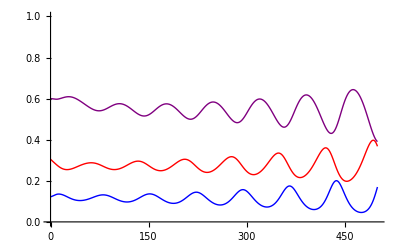

```mathematica
EpiPlot[20,20,500]
```

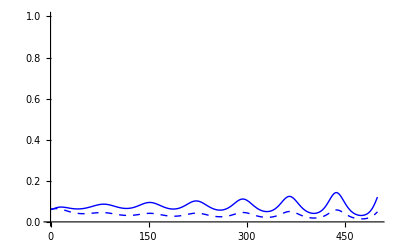

```mathematica
EpiPlot2[20,20,500]
```

Infections of pathogens of type 1 and infections of type 2 are in phase with one another.  This is in contrast to the case of Y=0 below where the lab between infections of type 1 and infections of type 2 vary over time generating allele frequency cycles.

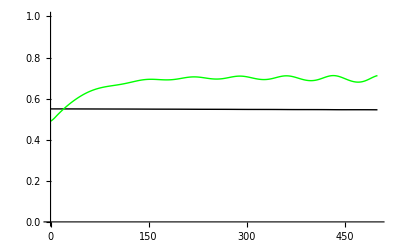

```mathematica
AFPlot[20,20,500]
```

Case when Y=0

## The Differential Equations

A special case of the full SIRS model presented above is the prefect-matching-alleles model in which hosts of type i can be only be infected by pathogens of type i.  Hence there are effectively only 2 infectious types of each class.  The full polymorphic equilibrium found above however includes a division by Y is therefore not valid when Y=0 and cannot be generalized to this case.

```mathematica
g1[h_,t_]:=b(s[h,t]+∑_(j=1)^nI i[h,j,t]+∑_(j=1)^nR r[h,j,t])(1-κ(∑_(k=1)^2 (s[k,t]+∑_(j=1)^nI i[k,j,t]+∑_(j=1)^nR r[k,j,t])))-d s[h,t]+nR/τR r[h,nR,t]-β s[h,t]∑_(j=1)^nI (i[h,j,t])
```

```mathematica
g2[h_,c_,t_]:=If[c==1,β s[h,t]∑_(j=1)^nI (i[h,j,t])-(δ+nI/τI)i[h,c,t],nI/τI i[h,c-1,t]-(δ+nI/τI)i[h,c,t]]
```

```mathematica
g3[h_,c_,t_]:=If[c==1,nI/τI i[h,nI,t]-(d+nR/τR)r[h,c,t],nR/τR r[h,c-1,t]-(d+nR/τR)r[h,c,t]]
```

## The Equilibria

At equilibrium the following equations must be satisfied.

```mathematica
EquiEqus[nIs_,nRs_]:=Join[Table[g1[h,∞]==0,{h,1,2}],Flatten[Table[g2[h,c,∞]==0,{h,1,2},{c,1,nIs}]],Flatten[Table[g3[h,c,∞]==0,{h,1,2},{c,1,nRs}]]]/.{nI->nIs,nR->nRs}
```

### The Disease free equilibrium

Simplifying the system of equations given that there are no disease types are present at equilibrium

```mathematica
EquiEqusDF[nIs_,nRs_]:=EquiEqus[nIs,nRs]/.Flatten[Join[Table[i[h,c,∞]->0,{h,1,2},{c,1,nIs}],Table[r[h,c,∞]->0,{h,1,2},{c,1,nIs}]]]
```

Only the susceptible equations are not satisfied for example:

```mathematica
EquiEqusDF[2,2]
```

{-d s[1,∞]+b s[1,∞] (1-κ (s[1,∞]+s[2,∞]))==0,-d s[2,∞]+b s[2,∞] (1-κ (s[1,∞]+s[2,∞]))==0,True,True,True,True,True,True,True,True}

```mathematica
Solve[{-d s[1,∞]+b s[1,∞] (1-κ (s[1,∞]+s[2,∞]))==0,-d s[2,∞]+b s[2,∞] (1-κ (s[1,∞]+s[2,∞]))==0},{s[1,∞],s[2,∞]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{s[2,∞]→-(-b+d)/(b κ)-s[1,∞]},{s[1,∞]→0,s[2,∞]→0}}

### The Endemic equilibrium

As with the system above we can solve for simplify the equations for the equilibria by solving for everything in terms of the first infectious class and the susceptible class.  Specifically at equilibrium the recovered classes and 2 through nI^th infected class are given by:

```mathematica
re[h_,c_]:=(nR/(d τR+nR))^(c-1)(nI/τI(τR/(d τR+nR)))(nI/(δ τI+nI))^(nI-1)ie1[h]
ie[h_,c_]:=(nI/(δ τI+nI))^(c-1)ie1[h]
```

where ie1[h] is the equilibrium number of hosts of type h in the first infected class. 

We can simplify the remaining equations by writing ∑_(j=1)^nI (i[h,j,t])=zI ie1[h],  r[h,nR,t]=znR ie1[h], and ∑_(j=1)^nR r[k,j,t]=zR ie1[h]

```mathematica
zsub={zI->Sum[ie[h,c],{c,1,nI}]/ie[h,1],zR->Sum[re[h,c],{c,1,nR}]/ie[h,1],znR->re[h,nR]/ie[h,1]}//FullSimplify
```

{zI→-((nI+δ τI) (-1+(nI/(nI+δ τI))^nI))/(δ τI),zR→-(nI (nI/(nI+δ τI))^(-1+nI) (-1+(nR/(nR+d τR))^nR))/(d τI),znR→(nI (nI/(nI+δ τI))^(-1+nI) τR (nR/(nR+d τR))^nR)/(nR τI)}

This results in the following equations much must be equal to 0 at equilibrium.

```mathematica
G1[h_]:=b(se[h]+(zI+zR)(ie1[h]))(1-κ∑_(k=1)^2 (se[k]+(zI+zR)(ie1[k])))-d se[h]+nR/τR znR(ie1[h])-se[h]zI β ie1[h]
G2[h_]:=se[h]zI β(ie1[h])-(δ+nI/τI)ie1[h]
```

```mathematica
equs=Join[Table[G1[h]==0,{h,1,2}],Table[G2[h]==0,{h,1,2}]]
vars=Join[Table[se[h],{h,1,2}],Table[ie1[h],{h,1,2}]]
```

{(nR znR ie1[1])/τR-d se[1]-zI β ie1[1] se[1]+b ((zI+zR) ie1[1]+se[1]) (1-κ ((zI+zR) ie1[1]+(zI+zR) ie1[2]+se[1]+se[2]))==0,(nR znR ie1[2])/τR-d se[2]-zI β ie1[2] se[2]+b ((zI+zR) ie1[2]+se[2]) (1-κ ((zI+zR) ie1[1]+(zI+zR) ie1[2]+se[1]+se[2]))==0,-(δ+nI/τI) ie1[1]+zI β ie1[1] se[1]==0,-(δ+nI/τI) ie1[2]+zI β ie1[2] se[2]==0}

{se[1],se[2],ie1[1],ie1[2]}

```mathematica
sol=Solve[equs,vars]//Simplify;
```

Solve::svars: Equations may not give solutions for all "solve" variables.

We are particularly interested only in cases when both susceptible types and both infected types are present of which there are two.

```mathematica
equ1={se[1]->(nI+δ τI)/(zI β τI),se[2]->(nI+δ τI)/(zI β τI),ie1[1]->-1/(4 b zI^2 (zI+zR)^2 β^2 κ τI^2 τR)(-nR zI^2 znR β^2 τI^2+nI zI^2 β^2 τI τR+4 b nI zI^2 β κ τI τR+4 b nI zI zR β κ τI τR-b zI^3 β^2 τI^2 τR-b zI^2 zR β^2 τI^2 τR+zI^2 β^2 δ τI^2 τR+4 b zI^2 β δ κ τI^2 τR+4 b zI zR β δ κ τI^2 τR+√(zI^2 β^2 τI^2 (-8 b (zI+zR)^2 κ (nI+δ τI) (d zI β τI+b (2 nI κ-zI β τI+2 δ κ τI)) τR^2+(nR zI znR β τI-(nI (4 b zR κ+zI (β+4 b κ))+(zI β δ-b (zI+zR) (zI β-4 δ κ)) τI) τR)^2))),ie1[2]->-1/(4 b zI^2 (zI+zR)^2 β^2 κ τI^2 τR)(-nR zI^2 znR β^2 τI^2+nI zI^2 β^2 τI τR+4 b nI zI^2 β κ τI τR+4 b nI zI zR β κ τI τR-b zI^3 β^2 τI^2 τR-b zI^2 zR β^2 τI^2 τR+zI^2 β^2 δ τI^2 τR+4 b zI^2 β δ κ τI^2 τR+4 b zI zR β δ κ τI^2 τR+√(zI^2 β^2 τI^2 (-8 b (zI+zR)^2 κ (nI+δ τI) (d zI β τI+b (2 nI κ-zI β τI+2 δ κ τI)) τR^2+(nR zI znR β τI-(nI (4 b zR κ+zI (β+4 b κ))+(zI β δ-b (zI+zR) (zI β-4 δ κ)) τI) τR)^2)))};equ2={se[1]->(nI+δ τI)/(zI β τI),se[2]->(nI+δ τI)/(zI β τI),ie1[1]->1/(4 b zI^2 (zI+zR)^2 β^2 κ τI^2 τR)(nR zI^2 znR β^2 τI^2-nI zI^2 β^2 τI τR-4 b nI zI^2 β κ τI τR-4 b nI zI zR β κ τI τR+b zI^3 β^2 τI^2 τR+b zI^2 zR β^2 τI^2 τR-zI^2 β^2 δ τI^2 τR-4 b zI^2 β δ κ τI^2 τR-4 b zI zR β δ κ τI^2 τR+√(zI^2 β^2 τI^2 (-8 b (zI+zR)^2 κ (nI+δ τI) (d zI β τI+b (2 nI κ-zI β τI+2 δ κ τI)) τR^2+(nR zI znR β τI-(nI (4 b zR κ+zI (β+4 b κ))+(zI β δ-b (zI+zR) (zI β-4 δ κ)) τI) τR)^2))),ie1[2]->1/(4 b zI^2 (zI+zR)^2 β^2 κ τI^2 τR)(nR zI^2 znR β^2 τI^2-nI zI^2 β^2 τI τR-4 b nI zI^2 β κ τI τR-4 b nI zI zR β κ τI τR+b zI^3 β^2 τI^2 τR+b zI^2 zR β^2 τI^2 τR-zI^2 β^2 δ τI^2 τR-4 b zI^2 β δ κ τI^2 τR-4 b zI zR β δ κ τI^2 τR+√(zI^2 β^2 τI^2 (-8 b (zI+zR)^2 κ (nI+δ τI) (d zI β τI+b (2 nI κ-zI β τI+2 δ κ τI)) τR^2+(nR zI znR β τI-(nI (4 b zR κ+zI (β+4 b κ))+(zI β δ-b (zI+zR) (zI β-4 δ κ)) τI) τR)^2)))};
```

```mathematica
equiSub[nIs_,nRs_,pars_]:=Flatten[Join[Table[s[h,∞]->se[h],{h,1,2}],Table[i[h,c,∞]-> ie[h,c],{h,1,2},{c,1,nIs}],Table[r[h,c,∞]-> re[h,c],{h,1,2},{c,1,nRs}]]/.equ2/.zsub/.{nI->nIs,nR->nRs}]/.pars
```

## Numerically Integrating

```mathematica
Clear[ODEs,Vars,Inits,InitEqus,αSub]
```

Functions

```mathematica
ODEs[nIs_,nRs_,pars_]:=Flatten[Join[Table[D[s[h,t],t]==g1[h,t],{h,1,2}],Table[D[i[h,c,t],t]==g2[h,c,t],{h,1,2},{c,1,nIs}],Table[D[r[h,c,t],t]==g3[h,c,t],{h,1,2},{c,1,nRs}]]]/.{nI->nIs,nR->nRs}/.pars
```

```mathematica
Vars[nIs_,nRs_]:=Flatten[Join[Table[s[h,t],{h,1,2}],Table[i[h,c,t],{h,1,2},{c,1,nIs}],Table[r[h,c,t],{h,1,2},{c,1,nRs}]]]
```

```mathematica
InitEqus[pH_,pP_,nI_,nR_,pars_]:={pP==(i1 αH αP)/(i1 αH αP+i2),pH==(s1 αH+i1 αH αP+r1 αH)/(s1 αH+s2+i1 αH αP+i2+r1 αH+r2)}/.{s1->s[1,∞], s2->s[2,∞],i1->Sum[i[1,c,∞],{c,1,nI}],i2->Sum[i[2,c,∞],{c,1,nI}],r1-> Sum[r[1,c,∞],{c,1,nR}],r2-> Sum[r[2,c,∞],{c,1,nR}]}/.equiSub[nI,nR,pars]
```

```mathematica
αSub[nI_,nR_,pars_]:=NSolve[InitEqus[0.55,0.45,nI,nR,pars],{αH,αP}]//Flatten
```

```mathematica
Inits[nIs_,nRs_,pars_]:=Block[{nI,nR,inits,h,p,c,equ},inits={};nI=nIs;nR=nRs; 
equ=equiSub[nI,nR,pars];
AppendTo[inits,s[1,0]==(s[1,∞]/.equ)*αH];
AppendTo[inits,s[2,0]==(s[2,∞]/.equ)];
For[c=1,c≤nI,c++,
AppendTo[inits,i[1,c,0]==(i[1,c,∞]/.equ)αH αP];
AppendTo[inits,i[2,c,0]==(i[2,c,∞]/.equ)];
];
For[c=1,c≤nR,c++,
AppendTo[inits,r[1,c,0]==(r[1,c,∞]/.equ)αH];
AppendTo[inits,r[2,c,0]==(r[2,c,∞]/.equ)];
];
inits/.αSub[nI,nR,pars]
]
```

Numerically integrating

```mathematica
nInt[nI_,nR_,pars_,tmax_]:=NDSolve[Join[ODEs[nI,nR,pars],Inits[nI,nR,pars]],Vars[nI,nR],{t,0,tmax}]//Flatten
```

#### Plots

Epidemic dynamics (Density of susceptible, infected, and recovered hosts)

```mathematica
EpiPlot[nI_,nR_,tmax_]:=Plot[{Sum[ssol[h,t],{h,1,2}],Sum[isol[h,c,t],{h,1,2},{c,1,nI}],Sum[rsol[h,c,t],{h,1,2},{c,1,nR}]},{t,1,tmax},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Purple}}]
```

Synchronization of infection types (Density of susceptible host type 1 and type 2)

```mathematica
EpiPlot2[nI_,nR_,tmax_]:=Plot[{Sum[isol[1,c,t],{c,1,nI}],Sum[isol[2,c,t],{c,1,nI}]},{t,1,tmax},PlotStyle->{{Thick,Blue},{Thick,Blue,Dashed}}]
```

```mathematica
AFPlot[nI_,nR_,tmax_]:=Plot[{(ssol[1,t]+Sum[isol[1,c,t],{c,1,nI}]+Sum[rsol[1,c,t],{c,1,nR}])/Sum[ssol[h,t]+Sum[isol[h,c,t],{c,1,nI}]+Sum[rsol[h,c,t],{c,1,nR}],{h,1,2}],Sum[isol[1,c,t],{c,1,nI}]/Sum[Sum[isol[h,c,t],{c,1,nI}],{h,1,2}]},{t,1,tmax},PlotStyle->{{Thick,Black},{Thick,Green}},PlotRange->All]
```

#### Example

```mathematica
Pars={b->0.02,d->0.001,δ->0.005,κ->1,τI->10,τR->50,β->0.8};
```

```mathematica
nsol=nInt[20,20,Pars,1000];
ssol[h_,τ_]:=s[h,t]/.nsol/.t->τ
isol[h_,c_,τ_]:=i[h,c,t]/.nsol/.t->τ
rsol[h_,c_,τ_]:=r[h,c,t]/.nsol/.t->τ
```

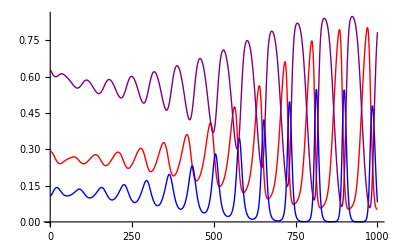

```mathematica
EpiPlot[20,20,1000]
```

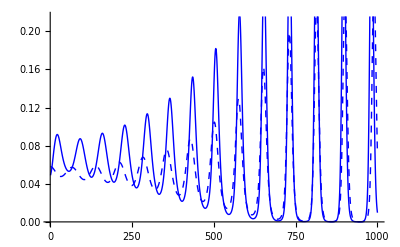

```mathematica
EpiPlot2[20,20,1000]
```

Unlike the case where Y>0, the density of infections of type 1 and type 2 are not in phase.  Instead the lag between the two types varies over time generating the variable amplitude allele frequency cycles over time seen below.

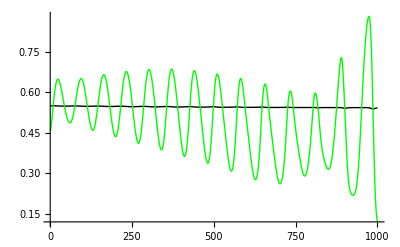

```mathematica
AFPlot[20,20,1000]
```

## Stability

As with the case where Y>0, we wish to confirm that in cases where the biologically valid endemic equilibrium is unstable with limit cycles that there are no allele frequency cycles:

### The Jacobian

```mathematica
Jmtrx[nIs_,nRs_,pars_]:=Block[{jmtrx,nI,nR,h,c,k,j,row},nI=nIs; nR=nRs; jmtrx=Table[{},{j,1,2+2nI+2nR}];
For[h=1,h≤2,h++,row=h;
For[k=1,k≤2,k++,AppendTo[jmtrx[[row]],D[g1[h,t],s[k,t]]]];
For[k=1,k≤2,k++,For[j=1,j≤nI,j++,AppendTo[jmtrx[[row]],D[g1[h,t],i[k,j,t]]]]];
For[k=1,k≤2,k++,For[j=1,j≤nR,j++,AppendTo[jmtrx[[row]],D[g1[h,t],r[k,j,t]]]]];
];
For[h=1,h≤2,h++,
For[c=1,c≤nI,c++,row=2+(h-1)nI+c;
For[k=1,k≤2,k++,AppendTo[jmtrx[[row]],D[g2[h,c,t],s[k,t]]]];
For[k=1,k≤2,k++,For[j=1,j≤nI,j++,AppendTo[jmtrx[[row]],D[g2[h,c,t],i[k,j,t]]]]];
For[k=1,k≤2,k++,For[j=1,j≤nR,j++,AppendTo[jmtrx[[row]],D[g2[h,c,t],r[k,j,t]]]]];
]];
For[h=1,h≤2,h++,
For[c=1,c≤nR,c++,row=2+2nI+(h-1)nR+c;
For[k=1,k≤2,k++,AppendTo[jmtrx[[row]],D[g3[h,c,t],s[k,t]]]];
For[k=1,k≤2,k++,For[j=1,j≤nI,j++,AppendTo[jmtrx[[row]],D[g3[h,c,t],i[k,j,t]]]]];
For[k=1,k≤2,k++,For[j=1,j≤nR,j++,AppendTo[jmtrx[[row]],D[g3[h,c,t],r[k,j,t]]]]];
]];
jmtrx/.pars/.{t->∞}
]
```

### The Disease Free Equilibrium

### The Endemic Equilibrium

#### Eigenvalue analysis

```mathematica
Max[Re[Eigenvalues[Jmtrx[20,20,Pars]/.equiSub[20,20,Pars]]]]
```

0.00447925

For the parameter combination (Pars) tested the endemic equilibrium is unstable

#### Eigenvector analysis

```mathematica
sys=Chop[Eigensystem[Jmtrx[20,20,Pars]/.equiSub[20,20,Pars]]];
```

Function for calculating allele frequencies given an eigenvector:

```mathematica
calcAF[nI_,nR_,evec_]:={(evec[[1]]+Sum[evec[[2+c]],{c,1,nI}]+Sum[evec[[2+2nI+c]],{c,1,nR}])/(evec[[1]]+evec[[2]]+Sum[evec[[2+(h-1)nI+c]],{h,1,2},{c,1,nI}]+Sum[evec[[2+2nI+(h-1)nR+c]],{h,1,2},{c,1,nR}]),(Sum[evec[[2+c]],{c,1,nI}])/(Sum[evec[[2+(h-1)nI+c]],{h,1,2},{c,1,nI}])}
```

Testing all eigenvectors corresponding to positive eigenvalues.

```mathematica
Module[{j},PosEvecs={};For[j=1,j≤Length[sys[[1]]],j++,
If[Re[sys[[1,j]]]>0,AppendTo[PosEvecs,sys[[2,j]]];Print[sys[[1,j]]];Print[Chop[calcAF[20,20,PosEvecs[[-1]]]]]
]]]
```

0.00447925+0.0897732 ⅈ

{-8.9889×10^8+2.04808×10^10 ⅈ,-1.91541×10^11-9.81792×10^10 ⅈ}

0.00447925-0.0897732 ⅈ

{-8.9889×10^8-2.04808×10^10 ⅈ,-1.91541×10^11+9.81792×10^10 ⅈ}

0.00432373+0.0897052 ⅈ

{0.5,0.5}

0.00432373-0.0897052 ⅈ

{0.5,0.5}

Reflecting the existence of allele-frequency cycles, there exists a positive eigenvalue where the eigenvector does not have allele frequencies of 0.5.